# Mie Theory Seminar

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
<<MaTeX`
```

/home/jonathan/Dropbox/Escuela/3.- Tesis/2.- Notas generales/2.- Teoría de Mie/0.- Cálculos

## Experimental data

```mathematica
FileNames["*.csv","0.- Respuestas del material"]
FileNames["*.txt","0.- Respuestas del material"]
```

{0.- Respuestas del material/Ag_nm.csv,0.- Respuestas del material/Au_2.csv,0.- Respuestas del material/H2O_nm.csv,0.- Respuestas del material/H2O_um.csv}

{0.- Respuestas del material/GAbajo_1000.txt,0.- Respuestas del material/GAbajo_100.txt,0.- Respuestas del material/GAbajo_10.txt,0.- Respuestas del material/GAbajo_500.txt}

### Water: G. M. Hale and M. R. Querry. (1973) “Optical constants of water in the 200-nm to 200-µm wavelength region”. Appl. Opt. 12, 555-563

```mathematica
files=FileNames["*.csv","0.- Respuestas del material"] 
nH2O = Import[files[[3]],"Data"]; (*1 es Ag, 2 es Au, 3 es en H2O en nm y 4 es en μm*) (* {nm, n, κ} donde N = n+iκ y ε = N^2   *) 
nH2O  = Drop[nH2O,1];
nH2O = Transpose[{ nH2O[[All,1]], nH2O[[All,2]]+I nH2O[[All,3]] }] (*N = {ω,n+iκ}) con n = Re(N), κ=Im(N) y además  N^2 = ε *)
nH2OFunc = Interpolation[nH2O]
nH2OPoints = Table[{nH2O[[i,1]]*(1+I), nH2O[[i,2]]},{i,Length[nH2O]}];
```

{0.- Respuestas del material/Ag_nm.csv,0.- Respuestas del material/Au_2.csv,0.- Respuestas del material/H2O_nm.csv,0.- Respuestas del material/H2O_um.csv}

{{200,1.396+1.1×10^-7 ⅈ},{225,1.373+4.9×10^-8 ⅈ},{250,1.362+3.35×10^-8 ⅈ},{275,1.354+2.35×10^-8 ⅈ},{300,1.349+1.6×10^-8 ⅈ},{325,1.346+1.08×10^-8 ⅈ},{350,1.343+6.5×10^-9 ⅈ},{375,1.341+3.5×10^-9 ⅈ},{400,1.339+1.86×10^-9 ⅈ},{425,1.338+1.3×10^-9 ⅈ},{450,1.337+1.02×10^-9 ⅈ},{475,1.336+9.35×10^-10 ⅈ},{500,1.335+1.×10^-9 ⅈ},{525,1.334+1.32×10^-9 ⅈ},{550,1.333+1.96×10^-9 ⅈ},{575,1.333+3.6×10^-9 ⅈ},{600,1.332+1.09×10^-8 ⅈ},{625,1.332+1.39×10^-8 ⅈ},{650,1.331+1.64×10^-8 ⅈ},{675,1.331+2.23×10^-8 ⅈ},{700,1.331+3.35×10^-8 ⅈ},{725,1.33+9.15×10^-8 ⅈ},{750,1.33+1.56×10^-7 ⅈ},{775,1.33+1.48×10^-7 ⅈ},{800,1.329+1.25×10^-7 ⅈ},{825,1.329+1.82×10^-7 ⅈ},{850,1.329+2.93×10^-7 ⅈ},{875,1.328+3.91×10^-7 ⅈ},{900,1.328+4.86×10^-7 ⅈ},{925,1.328+1.06×10^-6 ⅈ},{950,1.327+2.93×10^-6 ⅈ},{975,1.327+3.48×10^-6 ⅈ},{1000,1.327+2.89×10^-6 ⅈ},{1200,1.324+9.89×10^-6 ⅈ},{1400,1.321+0.000138 ⅈ},{1600,1.317+0.0000855 ⅈ},{1800,1.312+0.000115 ⅈ},{2000,1.306+0.0011 ⅈ},{2200,1.296+0.000289 ⅈ},{2400,1.279+0.000956 ⅈ},{2600,1.242+0.00317 ⅈ},{2650,1.219+0.0067 ⅈ},{2700,1.188+0.019 ⅈ},{2750,1.157+0.059 ⅈ},{2800,1.142+0.115 ⅈ},{2850,1.149+0.185 ⅈ},{2900,1.201+0.268 ⅈ},{2950,1.292+0.298 ⅈ},{3000,1.371+0.272 ⅈ},{3050,1.426+0.24 ⅈ},{3100,1.467+0.192 ⅈ},{3150,1.483+0.135 ⅈ},{3200,1.478+0.0924 ⅈ},{3250,1.467+0.061 ⅈ},{3300,1.45+0.0368 ⅈ},{3350,1.432+0.0261 ⅈ},{3400,1.42+0.0195 ⅈ},{3450,1.41+0.0132 ⅈ},{3500,1.4+0.0094 ⅈ},{3600,1.385+0.00515 ⅈ},{3700,1.374+0.0036 ⅈ},{3800,1.364+0.0034 ⅈ},{3900,1.357+0.0038 ⅈ},{4000,1.351+0.0046 ⅈ},{4100,1.346+0.00562 ⅈ},{4200,1.342+0.00688 ⅈ},{4300,1.338+0.00845 ⅈ},{4400,1.334+0.0103 ⅈ},{4500,1.332+0.0134 ⅈ},{4600,1.33+0.0147 ⅈ},{4700,1.33+0.0157 ⅈ},{4800,1.33+0.015 ⅈ},{4900,1.328+0.0137 ⅈ},{5000,1.325+0.0124 ⅈ},{5100,1.322+0.0111 ⅈ},{5200,1.317+0.0101 ⅈ},{5300,1.312+0.0098 ⅈ},{5400,1.305+0.0103 ⅈ},{5500,1.298+0.0116 ⅈ},{5600,1.289+0.0142 ⅈ},{5700,1.277+0.0203 ⅈ},{5800,1.262+0.033 ⅈ},{5900,1.248+0.0622 ⅈ},{6000,1.265+0.107 ⅈ},{6100,1.319+0.131 ⅈ},{6200,1.363+0.088 ⅈ},{6300,1.357+0.057 ⅈ},{6400,1.347+0.0449 ⅈ},{6500,1.339+0.0392 ⅈ},{6600,1.334+0.0356 ⅈ},{6700,1.329+0.0337 ⅈ},{6800,1.324+0.0327 ⅈ},{6900,1.321+0.0322 ⅈ},{7000,1.317+0.032 ⅈ},{7100,1.314+0.032 ⅈ},{7200,1.312+0.0321 ⅈ},{7300,1.309+0.0322 ⅈ},{7400,1.307+0.0324 ⅈ},{7500,1.304+0.0326 ⅈ},{7600,1.302+0.0328 ⅈ},{7700,1.299+0.0331 ⅈ},{7800,1.297+0.0335 ⅈ},{7900,1.294+0.0339 ⅈ},{8000,1.291+0.0343 ⅈ},{8200,1.286+0.0351 ⅈ},{8400,1.281+0.0361 ⅈ},{8600,1.275+0.0372 ⅈ},{8800,1.269+0.0385 ⅈ},{9000,1.262+0.0399 ⅈ},{9200,1.255+0.0415 ⅈ},{9400,1.247+0.0433 ⅈ},{9600,1.239+0.0454 ⅈ},{9800,1.229+0.0479 ⅈ},{10000,1.218+0.0508 ⅈ},{10500,1.185+0.0662 ⅈ},{11000,1.153+0.0968 ⅈ},{11500,1.126+0.142 ⅈ},{12000,1.111+0.199 ⅈ},{12500,1.123+0.259 ⅈ},{13000,1.146+0.305 ⅈ},{13500,1.177+0.343 ⅈ},{14000,1.21+0.37 ⅈ},{14500,1.241+0.388 ⅈ},{15000,1.27+0.402 ⅈ},{15500,1.297+0.414 ⅈ},{16000,1.325+0.422 ⅈ},{16500,1.351+0.428 ⅈ},{17000,1.376+0.429 ⅈ},{17500,1.401+0.429 ⅈ},{18000,1.423+0.426 ⅈ},{18500,1.443+0.421 ⅈ},{19000,1.461+0.414 ⅈ},{19500,1.476+0.404 ⅈ},{20000,1.48+0.393 ⅈ},{21000,1.487+0.382 ⅈ},{22000,1.5+0.373 ⅈ},{23000,1.511+0.367 ⅈ},{24000,1.521+0.361 ⅈ},{25000,1.531+0.356 ⅈ},{26000,1.539+0.35 ⅈ},{27000,1.545+0.344 ⅈ},{28000,1.549+0.338 ⅈ},{29000,1.551+0.333 ⅈ},{30000,1.551+0.328 ⅈ},{32000,1.546+0.324 ⅈ},{34000,1.536+0.329 ⅈ},{36000,1.527+0.343 ⅈ},{38000,1.522+0.361 ⅈ},{40000,1.519+0.385 ⅈ},{42000,1.522+0.409 ⅈ},{44000,1.53+0.436 ⅈ},{46000,1.541+0.462 ⅈ},{48000,1.555+0.488 ⅈ},{50000,1.587+0.514 ⅈ},{60000,1.703+0.587 ⅈ},{70000,1.821+0.576 ⅈ},{80000,1.886+0.547 ⅈ},{90000,1.924+0.536 ⅈ},{100000,1.957+0.532 ⅈ},{110000,1.966+0.531 ⅈ},{120000,2.004+0.526 ⅈ},{130000,2.036+0.514 ⅈ},{140000,2.056+0.5 ⅈ},{150000,2.069+0.495 ⅈ},{160000,2.081+0.496 ⅈ},{170000,2.094+0.497 ⅈ},{180000,2.107+0.499 ⅈ},{190000,2.119+0.501 ⅈ},{200000,2.13+0.504 ⅈ}}

InterpolatingFunction[…]

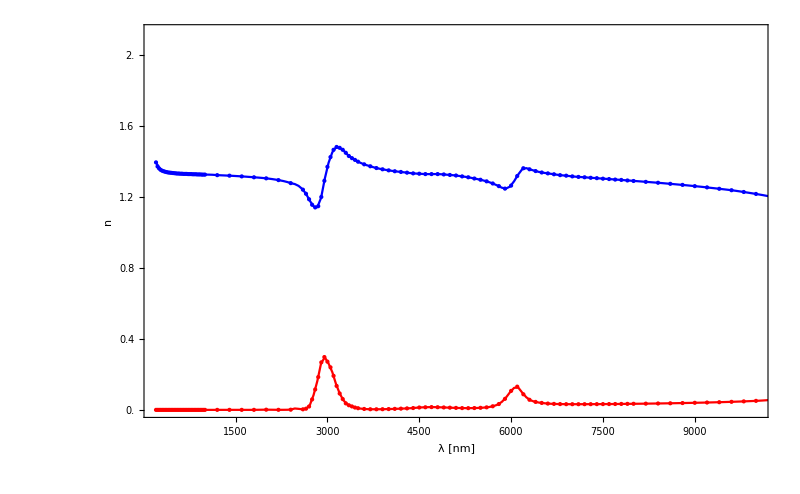

```mathematica
ListPlot[{Re[nH2OPoints],Im[nH2OPoints]}, PlotStyle->{Directive[Blue,PointSize[Large]],Directive[Red,PointSize[Large]]},Axes-> False];
Plot[{Re[nH2OFunc[λ]],Im[nH2OFunc[λ]]},{λ,200,200000},PlotStyle->{Blue,Red},Axes-> False];

Show[{%,%%},PlotStyle-> {Red,Blue}, Frame-> True,PlotRange-> {{200,10000},Automatic},
	FrameStyle-> {{Directive[Blue,Thickness[0.0035]],Directive[Red,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
	 FrameLabel->{{Style["n",20, Bold],Style["κ",20, Bold]},{Style["λ [nm]",20,Bold], Null}}, RotateLabel-> False,
	FrameTicks->{{Table[i,{i,0,2.5,.2}],Table[i,{i,0,2.5,.2}]},{Automatic,None}},
	FrameTicksStyle->{{Directive[14,Bold],Directive[14,Bold]},{Directive[14,Bold],FrameTicksStyle->Directive[14,Bold]}},ImageSize-> 800,
	Epilog->{Inset[Style["Hale & Querry (1973)", 24, Bold], {165000,1.85}],
			Inset[Style["N_H2O = n+iκ", 16], {165000,1.7}]}]
```

### Au: Johnson, P. B.; Christy, R. W. (1972). ”Optical Constants of the Noble Metals”. Physical Review B. 6 (12): 4370–4379

```mathematica
files=FileNames["*.csv","0.- Respuestas del material"]  
nAueV = Import[files[[2]],"Data"] ;(*1 es Ag, 2 es Au, 3 es en H2O en nm y 4 es en μm*) (* {nm, n, κ} donde N = n+iκ y ε = N^2   *) 
nAueV  = Drop[Drop[nAueV,-4],2]
```

{0.- Respuestas del material/Ag_nm.csv,0.- Respuestas del material/Au_2.csv,0.- Respuestas del material/H2O_nm.csv,0.- Respuestas del material/H2O_um.csv}

{{0.64,0.92,13.78},{0.77,0.56,11.21},{0.89,0.43,9.519},{1.02,0.35,8.145},{1.14,0.27,7.15},{1.26,0.22,6.35},{1.39,0.17,5.663},{1.51,0.16,5.083},{1.64,0.14,4.542},{1.76,0.13,4.103},{1.88,0.14,3.697},{2.01,0.21,3.272},{2.13,0.29,2.863},{2.26,0.43,2.455},{2.38,0.62,2.081},{2.5,1.04,1.833},{2.63,1.31,1.849},{2.75,1.38,1.914},{2.88,1.45,1.948},{3.,1.46,1.958},{3.12,1.47,1.952},{3.25,1.46,1.933},{3.37,1.48,1.895},{3.5,1.5,1.866},{3.62,1.48,1.871},{3.74,1.48,1.883},{3.87,1.54,1.898},{3.99,1.53,1.893},{4.12,1.53,1.889},{4.24,1.49,1.878},{4.36,1.47,1.869},{4.49,1.43,1.847},{4.61,1.38,1.803},{4.74,1.35,1.749},{4.86,1.33,1.688},{4.98,1.33,1.631},{5.11,1.32,1.577},{5.23,1.32,1.536},{5.36,1.3,1.497},{5.48,1.31,1.46},{5.6,1.3,1.427},{5.73,1.3,1.387},{5.85,1.3,1.35},{5.98,1.3,1.304},{6.1,1.33,1.277},{6.22,1.33,1.251},{6.35,1.34,1.226},{6.47,1.32,1.203},{6.6,1.28,1.188}}

```mathematica
h = 4.13566733*^-15 (* eV s *);  c = 3*^17 (*nm s^-1*) ;
(*E =hν=hc/λ -> λ = hc/E *)
nAu = Transpose[{ h c/nAueV[[All,1]], nAueV[[All,2]]+I nAueV[[All,3]] }] (*N = {ω,n+iκ}) con n = Re(N), κ=Im(N) y además  N^2 = ε *)
nAuFunc = Interpolation[nAu]
```

{{1938.59,0.92+13.78 ⅈ},{1611.3,0.56+11.21 ⅈ},{1394.05,0.43+9.519 ⅈ},{1216.37,0.35+8.145 ⅈ},{1088.33,0.27+7.15 ⅈ},{984.683,0.22+6.35 ⅈ},{892.59,0.17+5.663 ⅈ},{821.656,0.16+5.083 ⅈ},{756.525,0.14+4.542 ⅈ},{704.943,0.13+4.103 ⅈ},{659.947,0.14+3.697 ⅈ},{617.264,0.21+3.272 ⅈ},{582.488,0.29+2.863 ⅈ},{548.982,0.43+2.455 ⅈ},{521.303,0.62+2.081 ⅈ},{496.28,1.04+1.833 ⅈ},{471.749,1.31+1.849 ⅈ},{451.164,1.38+1.914 ⅈ},{430.799,1.45+1.948 ⅈ},{413.567,1.46+1.958 ⅈ},{397.66,1.47+1.952 ⅈ},{381.754,1.46+1.933 ⅈ},{368.16,1.48+1.895 ⅈ},{354.486,1.5+1.866 ⅈ},{342.735,1.48+1.871 ⅈ},{331.738,1.48+1.883 ⅈ},{320.594,1.54+1.898 ⅈ},{310.952,1.53+1.893 ⅈ},{301.141,1.53+1.889 ⅈ},{292.618,1.49+1.878 ⅈ},{284.564,1.47+1.869 ⅈ},{276.325,1.43+1.847 ⅈ},{269.132,1.38+1.803 ⅈ},{261.751,1.35+1.749 ⅈ},{255.288,1.33+1.688 ⅈ},{249.137,1.33+1.631 ⅈ},{242.798,1.32+1.577 ⅈ},{237.228,1.32+1.536 ⅈ},{231.474,1.3+1.497 ⅈ},{226.405,1.31+1.46 ⅈ},{221.554,1.3+1.427 ⅈ},{216.527,1.3+1.387 ⅈ},{212.086,1.3+1.35 ⅈ},{207.475,1.3+1.304 ⅈ},{203.393,1.33+1.277 ⅈ},{199.469,1.33+1.251 ⅈ},{195.386,1.34+1.226 ⅈ},{191.762,1.32+1.203 ⅈ},{187.985,1.28+1.188 ⅈ}}

InterpolatingFunction[…]

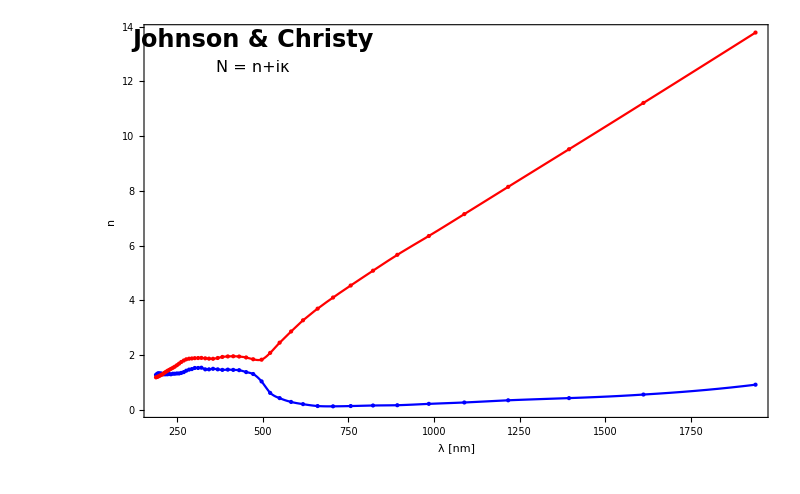

```mathematica
ListPlot[{Re[nAu],Transpose[{nAu[[All,1]],Im[nAu[[All,2]]]}]}, PlotStyle->{Directive[Blue,PointSize[Large]],Directive[Red,PointSize[Large]]},Axes-> False];
Plot[{Re[nAuFunc[λ]],Im[nAuFunc[λ]]},{λ,188,1940},PlotStyle->{Blue,Red},Axes-> False];
Show[{%,%%},PlotStyle-> {Red,Blue}, Frame-> True,
	FrameStyle-> {{Directive[Blue,Thickness[0.0035]],Directive[Red,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
	 FrameLabel->{{Style["n",20, Bold],Style["κ",20, Bold]},{Style["λ [nm]",20,Bold], Null}}, RotateLabel-> False,
	FrameTicks->{{Table[i,{i,0,14,2}],Table[i,{i,0,14,2}]},{Automatic,None}},
	FrameTicksStyle->{{Directive[14,Bold],Directive[14,Bold]},{Directive[14,Bold],FrameTicksStyle->Directive[14,Bold]}},ImageSize-> 800,
	Epilog->{Inset[Style["Johnson & Christy", 24, Bold], {470,13.5}],
			Inset[Style["N = n+iκ", 16], {470,12.5}]}]
```

### Ag: P. B. Johnson and R. W. Christy. Optical Constants of the Noble Metals, Phys. Rev. B 6, 4370-4379 (1972)

```mathematica
files=FileNames["*.csv","0.- Respuestas del material"]
nAg = Import[files[[1]],"Data"]; (*1 es Ag, 2 es Au ,3 es en H2O en nm y 4 es en μm*) (* {nm, n, κ} donde N = n+iκ y ε = N^2   *) 
nAg  = Drop[nAg,1];
nAg = Transpose[{ nAg[[All,1]], nAg[[All,2]]+I nAg[[All,3]] }] (*N = {ω,n+iκ}) con n = Re(N), κ=Im(N) y además  N^2 = ε *)
nAgFunc = Interpolation[nAg]
nAgPoints = Table[{nAg[[i,1]]*(1+I), nAg[[i,2]]},{i,Length[nAg]}];
```

{0.- Respuestas del material/Ag_nm.csv,0.- Respuestas del material/Au_2.csv,0.- Respuestas del material/H2O_nm.csv,0.- Respuestas del material/H2O_um.csv}

{{187.9,1.07+1.212 ⅈ},{191.6,1.1+1.232 ⅈ},{195.3,1.12+1.255 ⅈ},{199.3,1.14+1.277 ⅈ},{203.3,1.15+1.296 ⅈ},{207.3,1.18+1.312 ⅈ},{211.9,1.2+1.325 ⅈ},{216.4,1.22+1.336 ⅈ},{221.4,1.25+1.342 ⅈ},{226.2,1.26+1.344 ⅈ},{231.3,1.28+1.357 ⅈ},{237.1,1.28+1.367 ⅈ},{242.6,1.3+1.378 ⅈ},{249,1.31+1.389 ⅈ},{255.1,1.33+1.393 ⅈ},{261.6,1.35+1.387 ⅈ},{268.9,1.38+1.372 ⅈ},{276.1,1.41+1.331 ⅈ},{284.4,1.41+1.264 ⅈ},{292.4,1.39+1.161 ⅈ},{300.9,1.34+0.964 ⅈ},{310.7,1.13+0.616 ⅈ},{320.4,0.81+0.392 ⅈ},{331.5,0.17+0.829 ⅈ},{342.5,0.14+1.142 ⅈ},{354.2,0.1+1.419 ⅈ},{367.9,0.07+1.657 ⅈ},{381.5,0.05+1.864 ⅈ},{397.4,0.05+2.07 ⅈ},{413.3,0.05+2.275 ⅈ},{430.5,0.04+2.462 ⅈ},{450.9,0.04+2.657 ⅈ},{471.4,0.05+2.869 ⅈ},{495.9,0.05+3.093 ⅈ},{520.9,0.05+3.324 ⅈ},{548.6,0.06+3.586 ⅈ},{582.1,0.05+3.858 ⅈ},{616.8,0.06+4.152 ⅈ},{659.5,0.05+4.483 ⅈ},{704.5,0.04+4.838 ⅈ},{756,0.03+5.242 ⅈ},{821.1,0.04+5.727 ⅈ},{892,0.04+6.312 ⅈ},{984,0.04+6.992 ⅈ},{1088,0.04+7.795 ⅈ},{1216,0.09+8.828 ⅈ},{1393,0.13+10.1 ⅈ},{1610,0.15+11.85 ⅈ},{1937,0.24+14.08 ⅈ}}

InterpolatingFunction[…]

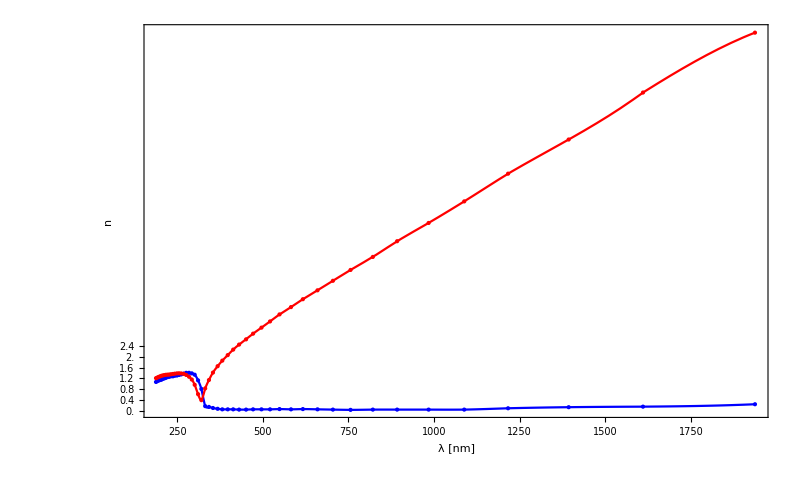

```mathematica
ListPlot[{Re[nAgPoints],Im[nAgPoints]}, PlotStyle->{Directive[Blue,PointSize[Large]],Directive[Red,PointSize[Large]]},Axes-> False];
Plot[{Re[nAgFunc[λ]],Im[nAgFunc[λ]]},{λ,188,1940},PlotStyle->{Blue,Red},Axes-> False];

Show[{%,%%},PlotStyle-> {Red,Blue}, Frame-> True,PlotRange->All,
	FrameStyle-> {{Directive[Blue,Thickness[0.0035]],Directive[Red,Thickness[0.0035]]},{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}},
	 FrameLabel->{{Style["n",20, Bold],Style["κ",20, Bold]},{Style["λ [nm]",20,Bold], Null}}, RotateLabel-> False,
	FrameTicks->{{Table[i,{i,0,2.4,.2}],Table[i,{i,0,15,1}]},{Automatic,None}},
	FrameTicksStyle->{{Directive[14,Bold],Directive[14,Bold]},{Directive[14,Bold],FrameTicksStyle->Directive[14,Bold]}},ImageSize-> 800,
	Epilog->{Inset[Style["Johnson & Christy (1973)", 24, Bold], {165000,1.85}],
			Inset[Style["N_Ag = n+iκ", 16], {165000,1.7}]}]
```

## Usefull functions

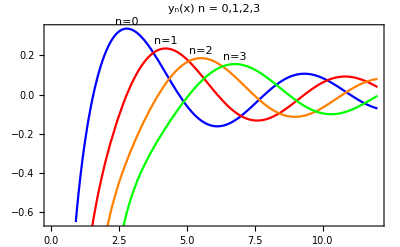
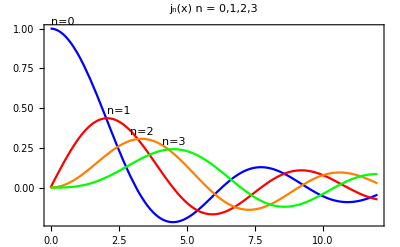

```mathematica
color = {Blue, Red,Orange, Green, Purple, Pink};
orden = Table[i,{i,0,3}];

Show[Plot[SphericalBesselJ[orden[[#]],z],{z,0,12}, PlotLabels->Placed["n="<>ToString [orden[[#]]],Above], PlotStyle-> color[[#]]] &/@Table[i,{i,Length[orden]}],Frame-> True, PlotLabel-> "j_n(x)\n n = 0,1,2,3"];
Show[Plot[SphericalBesselY[orden[[#]],z],{z,0,12}, PlotLabels->Placed["n="<>ToString [orden[[#]]],Above], PlotStyle-> color[[#]]] &/@Table[i,{i,Length[orden]}],Frame-> True,PlotLabel-> "y_n(x)\n n = 0,1,2,3"];
Row[{%,%%}]
```

```mathematica
derivada[xlist_,ylist_]:= Table[{xlist[[i]],(1/12 ylist[[i-2]]-2/3 ylist[[i-1]]+2/3 ylist[[i+1]]-1/12 ylist[[i+2]])/(xlist[[i+1]]-xlist[[i]])},{i,3,Length[xlist]-2}]
```

```mathematica
legendSquare [list_,orientation_,position_]:=  (*position is a 2 elements list*)
Placed[LineLegend[list,LegendLayout-> orientation,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->5,LabelStyle->{FontSize->20, FontFamily-> "Helvetica Neue"},
LegendMarkerSize-> {30,15},
LegendMarkers->Graphics[{Thickness[0.5],Line[{{-2,0},{2,0}}]}]],position]
(*position list can be build with: Bottom, Left, Center, Right, Top, Tooltip, StatusArea or given coordinates*)
```

## Mie Coefficients, Q_sca & Q_ext

### Coefficients (a_n & b_n)

http://functions.wolfram.com/Bessel-TypeFunctions/SphericalBesselJ/20/ShowAll.html
 d/dz f_n(z) = f_(n-1)(z) - (n+1)/z f_n(z)
 						d/dz g_n(z)  = f_n(z) +z d/dz f_n(z)
							 = f_n(z) +  z (f_(n-1)(z) - (n+1)/z f_n(z))
							=  f_n(z) +  z f_(n-1)(z) - (n+1)f_n(z)
							=  z f_(n-1)(z) +(1+- n-1)f_n(z)
							= z f_(n-1)(z) - n f_n(z)

```mathematica
rbψ[n_,z_] := z *SphericalBesselJ[n,z]
rbξ[n_,z_] := z *SphericalHankelH1[n,z]
drbψ[n_,z_]:=-n *SphericalBesselJ[n,z]+ z * SphericalBesselJ[n-1,z]  
drbξ[n_,z_]:=-n * SphericalHankelH1[n,z] + z* SphericalHankelH1[n-1,z]
```

```mathematica
mieCoef[n_,indexes_,λ_,rad_]:= Module[{m,an,bn,x},  (*si n es una lista -> {{Subscript[a, 1], Subscript[a, 2],...,Subscript[a, n]},{Subscript[b, 1], Subscript[b, 2],...,Subscript[b, n]}}, si no, sólo da la pareja*)
m = indexes[[2]]/indexes[[1]];   (*Partícula / medio*)
x = 2* π *indexes[[1]] *rad / λ;
an = (m rbψ[n, m x]drbψ[n, x] - rbψ[n,x]drbψ[n,m x])/(m rbψ[n,m x]drbξ[n, x]-rbξ[n, x]drbψ[n, m x]);
bn = (rbψ[n, m x]drbψ[n, x] -m rbψ[n,x]drbψ[n,m x])/(rbψ[n,m x]drbξ[n, x]-m rbξ[n, x]drbψ[n, m x]);
{an,bn}]
```

### Q_sca & Q_ext

```mathematica
scaCQ[nmax_,indexes_,λ_,rad_]:= Module[{an,bn,sum},
{an,bn} = mieCoef[Table[i,{i,nmax}],indexes,λ,rad];
sum = Sum[(2*i+1)* (Abs[an[[i]] ]^2+Abs[bn[[i]] ]^2),{i, Length[an]}];
sum = ((λ^2 )* sum)/(2*π*( Abs[indexes[[1]]]^2));
sum = sum / (π  *(rad^2))]
```

```mathematica
extCQ[nmax_,indexes_,λ_,rad_]:= Module[{sum,an,bn},
{an,bn} = mieCoef[Table[i,{i,nmax}],indexes,λ,rad];
sum = Sum[(2*i+1)* Re[ an[[i]] + bn[[i]]  ],{i, Length[an]}];
sum = ((λ^2 )* sum)/(2*π*( Abs[indexes[[1]]]^2));
sum = sum / (π  *(rad^2))]
```

### Q_sca & Q_ext, fixed n

```mathematica
scaCQnFixed[n_,indexes_,λ_,rad_]:= Module[{an,bn,sum},
{an,bn} = mieCoef[n,indexes,λ,rad];
sum = (2*n+1)* (Abs[an]^2+Abs[bn ]^2);
sum = ((λ^2 )* sum)/(2*π*( Abs[indexes[[1]]]^2));
sum = sum / (π  *(rad^2))]
```

```mathematica
extCQnFixed[n_,indexes_,λ_,rad_]:= Module[{sum,an,bn},
{an,bn} = mieCoef[n,indexes,λ,rad];
sum =(2*n+1)* Re[ an + bn ];
sum = ((λ^2 )* sum)/(2*π*( Abs[indexes[[1]]]^2));
sum = sum / (π  *(rad^2))]
```

## Graphs

### Water droplet

#### ( r = 1μm) (variating n )

```mathematica
color = {Blue, Red,Orange, Green, Purple, Pink}
(*orden = Table[i,{i,50,300,50}];*)
orden  = Table[i,{i,10,35,5}]
radio = 1*^3
```

{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0.5, 0],RGBColor[0, 1, 0],RGBColor[0.5, 0, 0.5],RGBColor[1, 0.5, 0.5]}

{10,15,20,25,30,35}

1000

```mathematica
AbsoluteTiming[Table[{1000/(λ),extCQ[#,{1.,nH2OFunc[λ]},λ,radio]},{λ,200.,2000.}]]&/@orden;
tiempo = %[[All,1]];
res = %%[[All,2]];
```

$Aborted

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

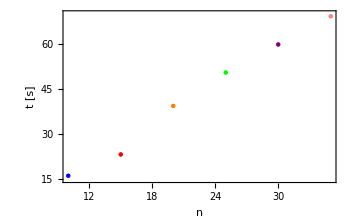
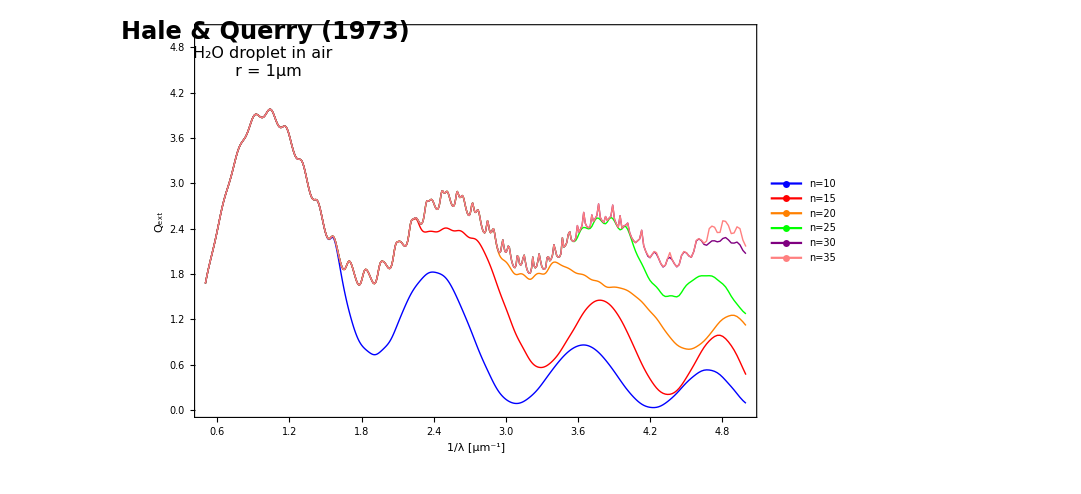

H2O_r_1000_n.pdf

```mathematica
Show[ListLinePlot[res, PlotStyle->Table[{Thick,color[[i]]},{i,Length[color]}],
	PlotLegends->legendSquare[Table["n="<>ToString[orden[[i]]],{i,Length[orden]}],"Row",{Left,Bottom}]],
		Frame-> True, PlotRange->{0,5},
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["Q_ext",24,Bold],Null},{Style["1/λ [μm^-1]",24, Bold], Null}}, 
		ImageSize-> 800,
		Epilog->{Inset[Style["Hale & Querry (1973)", 24, Bold], {1,5}],
			Inset[Style["H_2O droplet in air \n r = 1μm", 16], {1,4.6}]}];

Show[ListPlot[Table[{{orden[[i]],tiempo[[i]]}},{i,Length[tiempo]}],PlotStyle->Table[{PointSize[Large],color[[i]]},{i,Length[color]}]],
		Frame-> True,PlotRange-> {15,70},
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["t [s]",24,Bold],Null},{Style["n",24, Bold], Null}}, 
		ImageSize-> 350];

Overlay[{%,%%},Alignment->{Right,Top}]
Export["H2O_r_1000_n.pdf",%]
```

#### ( n = 35) (variating r )

```mathematica
color = {Blue, Red,Orange, Green, Purple, Pink}
(*orden = Table[i,{i,50,300,50}];*)
radio  = 1*^3  {1.,.75,.5,.25,.1}
orden = 35
```

{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0.5, 0],RGBColor[0, 1, 0],RGBColor[0.5, 0, 0.5],RGBColor[1, 0.5, 0.5]}

{1000.,750.,500.,250.,100.}

35

```mathematica
AbsoluteTiming[Table[{1000/(λ),extCQ[orden,{1.,nH2OFunc[λ]},λ,#]},{λ,200.,2000.}]]&/@radio;
tiempo = %[[All,1]];
res = %%[[All,2]];
```

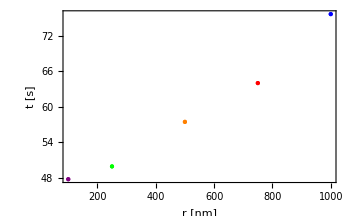
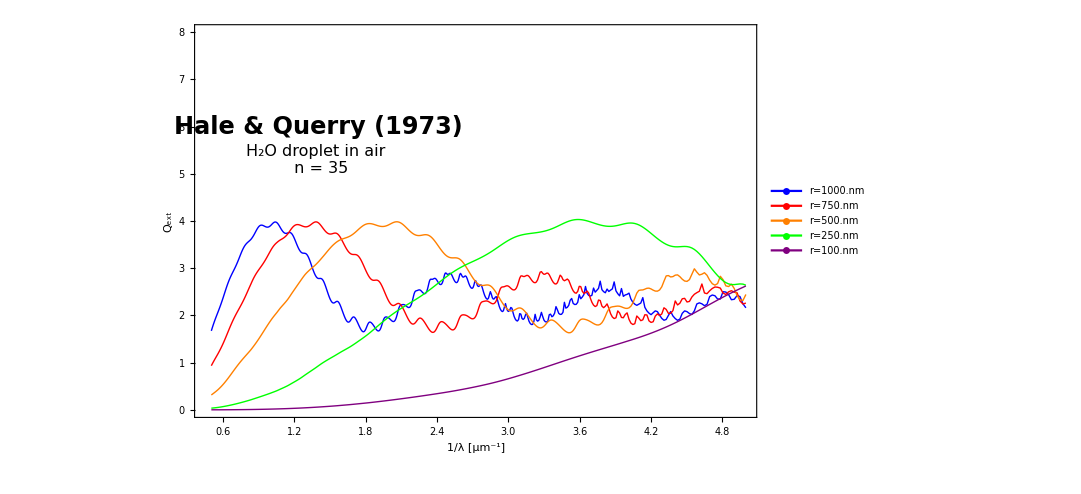

H2O_n_35_radii.pdf

```mathematica
Show[ListLinePlot[res, PlotStyle->Table[{Thick,color[[i]]},{i,Length[color]}],
	PlotLegends->legendSquare[Table["r="<>ToString[radio[[i]]]<>"nm",{i,Length[radio]}],"Row",{Left,Top}]],
		Frame-> True, PlotRange->{{.45,5},{0,8}},
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["Q_ext",24,Bold],Null},{Style["1/λ [μm^-1]",24, Bold], Null}}, 
		ImageSize-> 800,
		Epilog->{Inset[Style["Hale & Querry (1973)", 24, Bold], {1.4,6}],
			Inset[Style["H_2O droplet in air \n n = 35", 16], {1.4,5.3}]}];

Show[ListPlot[Table[{{radio[[i]],tiempo[[i]]}},{i,Length[tiempo]}],PlotStyle->Table[{PointSize[Large],color[[i]]},{i,Length[color]}]],
		Frame-> True,PlotRange-> All,
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["t [s]",24,Bold],Null},{Style["r [nm]",24, Bold], Null}}, 
		ImageSize-> 350];

Overlay[{%,%%},Alignment->{Right,Top}]
Export["H2O_n_35_radii.pdf",%]
```

### Au NP

```mathematica
color = {Blue, Red,Orange, Green, Purple, Pink}
```

{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0.5, 0],RGBColor[0, 1, 0],RGBColor[0.5, 0, 0.5],RGBColor[1, 0.5, 0.5]}

#### Garcia de Abajo’s Data

```mathematica
files=FileNames["*.txt","0.- Respuestas del material"]  
gAb = Import[files[[#]],"Data"] &/@{1,4,2,3};
rgAb = {1000,500,100,10};
```

{0.- Respuestas del material\GAbajo_1000.txt,0.- Respuestas del material\GAbajo_100.txt,0.- Respuestas del material\GAbajo_10.txt,0.- Respuestas del material\GAbajo_500.txt}

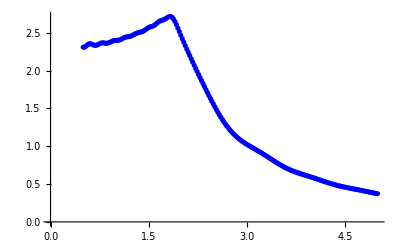
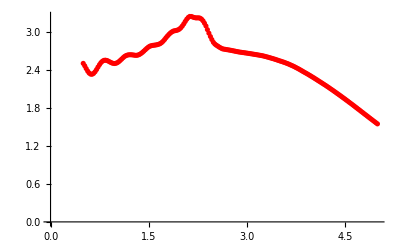
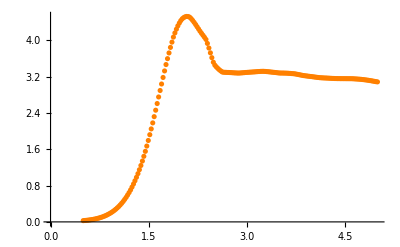
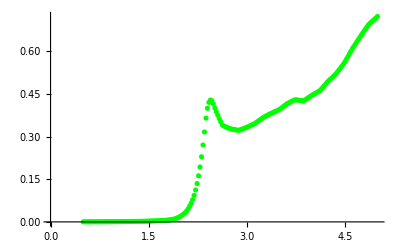

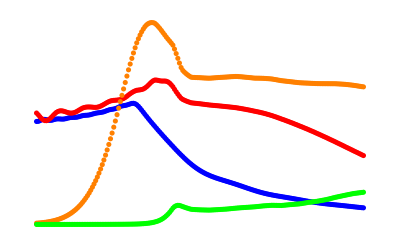

```mathematica
ListPlot[Transpose[{gAb[[#,All,1]],gAb[[#,All,2]]/(π rgAb[[#]]^2)}],PlotStyle->color[[#]]]&/@Table[i,{i,Length[gAb]}]
gAbajoData = Show[%,PlotRange-> All, Axes-> False]
```

#### ( r = 1000 nm) (variating n ) in air

```mathematica
orden  = Table[i,{i,10,35,5}]
radio= 1*^3
```

{10,15,20,25,30,35}

1000

```mathematica
AbsoluteTiming[Table[{h c/(λ),extCQ[#,{1.,nAuFunc[λ]},λ,radio]},{λ,250.,1880.}]]&/@orden;
tiempo = %[[All,1]];
res = %%[[All,2]];
```

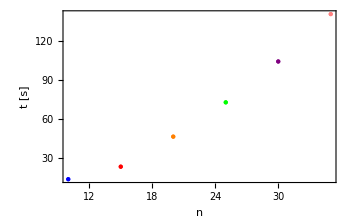
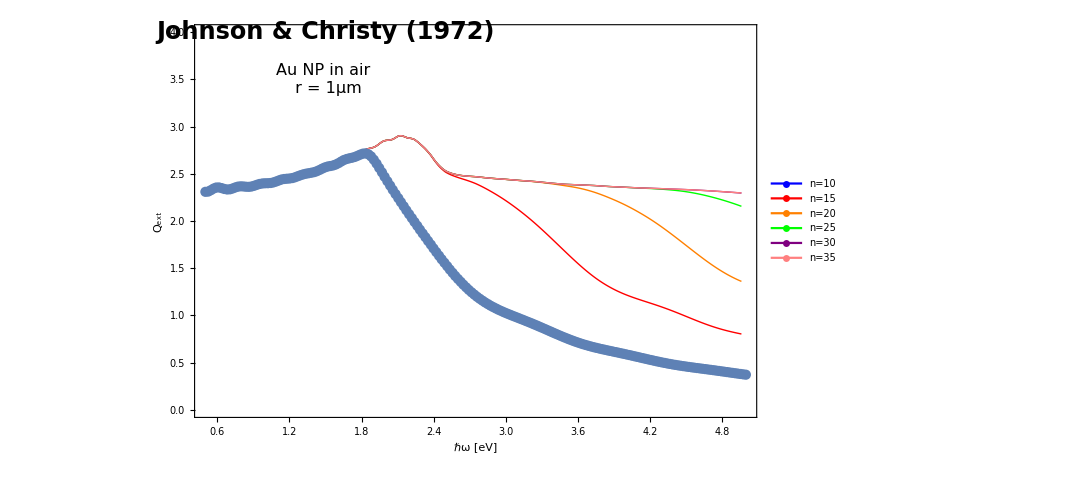

Au_r_1000_n_air.pdf

```mathematica
Show[{ListLinePlot[res, PlotStyle->Table[{Thick,color[[i]]},{i,Length[color]}],PlotRange->All,Axes-> False,
	PlotLegends->legendSquare[Table["n="<>ToString[orden[[i]]],{i,Length[orden]}],"Column",{Left,Bottom}]],
	ListPlot[Transpose[{gAb[[1,All,1]],gAb[[1,All,2]]/(π rgAb[[1]]^2)}], Axes-> False]},
		Frame-> True, PlotRange->{{.5,5},{0,4}},
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["Q_ext",24,Bold],Null},{Style["ℏω [eV]",24, Bold], Null}}, 
		ImageSize-> 800,
		Epilog->{Inset[Style["Johnson & Christy (1972)", 24, Bold], {1.5,4}],
			Inset[Style["Au NP in air \n r = 1μm", 16], {1.5,3.5}]}];

Show[ListPlot[Table[{{orden[[i]],tiempo[[i]]}},{i,Length[tiempo]}],PlotStyle->Table[{PointSize[Large],color[[i]]},{i,Length[color]}]],
		Frame-> True,PlotRange-> All,
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["t [s]",24,Bold],Null},{Style["n",24, Bold], Null}}, 
		ImageSize-> 350];

Overlay[{%,%%},Alignment->{Right,Top}]
Export["Au_r_1000_n_air.pdf",%]
```

#### ( n = 10) (variating r ) in air

```mathematica
radio  = rgAb 
orden = 10
```

{1000,500,100,10}

10

```mathematica
AbsoluteTiming[Table[{h c/(λ),extCQ[orden,{1.,nAuFunc[λ]},λ,#]},{λ,250.,1880.}]]&/@radio;
tiempo = %[[All,1]];
res = %%[[All,2]];
```

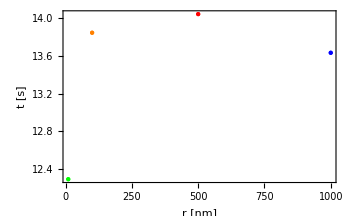
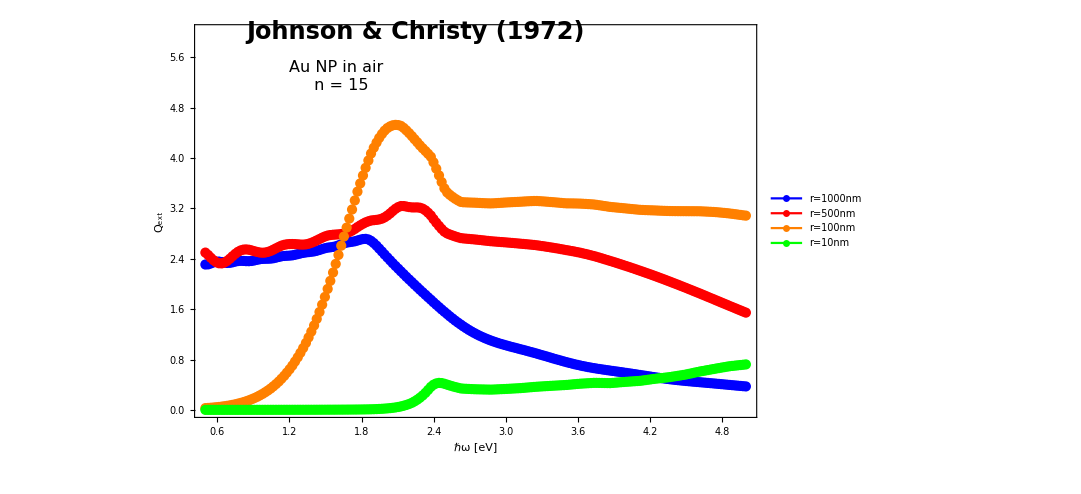

Au_n_15_radii_air.pdf

```mathematica
Show[{ListLinePlot[res, PlotStyle->Table[{Thick,color[[i]]},{i,Length[color]}],PlotRange->All,Axes-> False,
	PlotLegends->legendSquare[Table["r="<>ToString[radio[[i]]]<>"nm",{i,Length[radio]}],"Column",{Left,Top}]],
	gAbajoData},
		Frame-> True, PlotRange->{{.5,5},{0,6}},
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["Q_ext",24,Bold],Null},{Style["ℏω [eV]",24, Bold], Null}}, 
		ImageSize-> 800,
		Epilog->{Inset[Style["Johnson & Christy (1972)", 24, Bold], {2.25,6}],
			Inset[Style["Au NP in air \n n = 15", 16], {1.61,5.3}]}];

Show[ListPlot[Table[{{radio[[i]],tiempo[[i]]}},{i,Length[tiempo]}],PlotStyle->Table[{PointSize[Large],color[[i]]},{i,Length[color]}]],
		Frame-> True,PlotRange-> All,
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["t [s]",24,Bold],Null},{Style["r [nm]",20, Bold], Null}}, 
		ImageSize-> 350];

Overlay[{%,%%},Alignment->{Right,Top}]
Export["Au_n_15_radii_air.pdf",%]
```

### Ag NP

#### ( r = 1μm) (variating n )

```mathematica
color = {Blue, Red,Orange, Green, Purple, Pink}
(*orden = Table[i,{i,50,300,50}];*)
orden  = Table[i,{i,10,35,5}]
radio = 1*^3
```

{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0.5, 0],RGBColor[0, 1, 0],RGBColor[0.5, 0, 0.5],RGBColor[1, 0.5, 0.5]}

{10,15,20,25,30,35}

1000

```mathematica
AbsoluteTiming[Table[{h c/(λ),extCQ[#,{1.,nAgFunc[λ]},λ,radio]},{λ,188.,1935.}]]&/@orden;
tiempo = %[[All,1]];
res = %%[[All,2]];
```

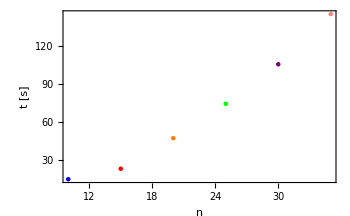
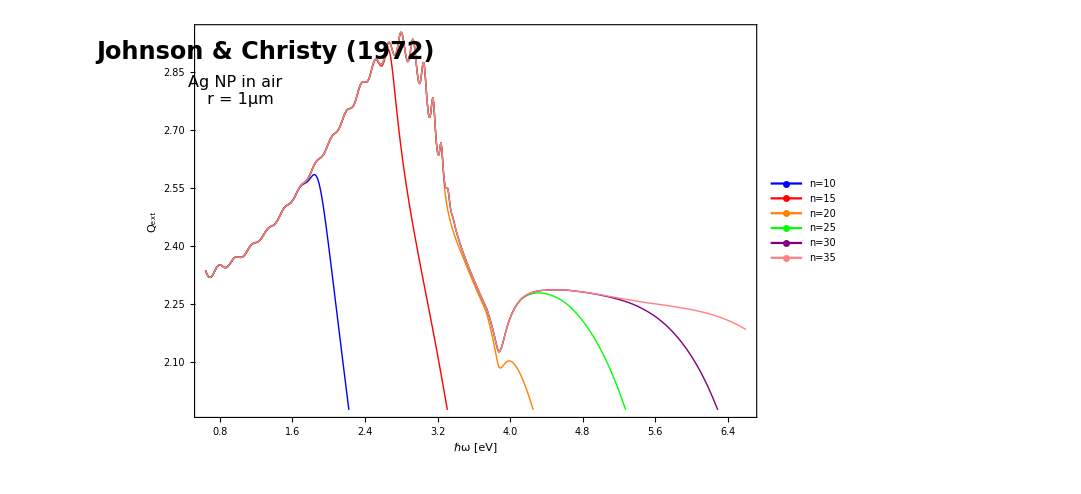

Ag_r_1000_n.pdf

```mathematica
Show[ListLinePlot[res, PlotStyle->Table[{Thick,color[[i]]},{i,Length[color]}],
	PlotLegends->legendSquare[Table["n="<>ToString[orden[[i]]],{i,Length[orden]}],"Row",{Left,Bottom}]],
		Frame-> True, PlotRange->All,
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["Q_ext",24,Bold],Null},{Style["ℏω [eV]",24, Bold], Null}}, 
		ImageSize-> 800,
		Epilog->{Inset[Style["Johnson & Christy (1972)", 24, Bold], {1.3,2.9}],
			Inset[Style["Ag NP in air \n r = 1μm", 16], {1,2.8}]}];

Show[ListPlot[Table[{{orden[[i]],tiempo[[i]]}},{i,Length[tiempo]}],PlotStyle->Table[{PointSize[Large],color[[i]]},{i,Length[color]}]],
		Frame-> True,PlotRange->Automatic,
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["t [s]",24,Bold],Null},{Style["n",24, Bold], Null}}, 
		ImageSize-> 350];

Overlay[{%,%%},Alignment->{Right,Top}]
Export["Ag_r_1000_n.pdf",%]
```

#### ( n = 35) (variating r )

```mathematica
color = {Blue, Red,Orange, Green, Purple, Pink}
(*orden = Table[i,{i,50,300,50}];*)
radio  = 1*^3  {1.,.5,.25,.1}
orden = 35
```

{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0.5, 0],RGBColor[0, 1, 0],RGBColor[0.5, 0, 0.5],RGBColor[1, 0.5, 0.5]}

{1000.,500.,250.,100.}

35

```mathematica
AbsoluteTiming[Table[{h c /(λ),extCQ[orden,{1.,nAgFunc[λ]},λ,#]},{λ,188.,1935.}]]&/@radio;
tiempo = %[[All,1]];
res = %%[[All,2]];
```

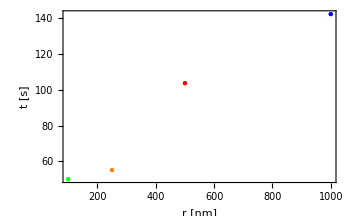
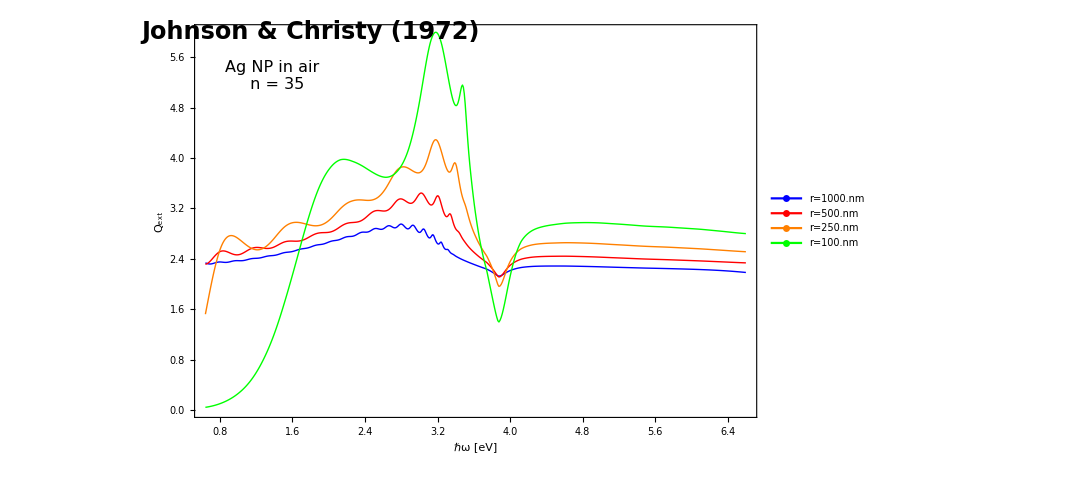

Ag_n_35_radii.pdf

```mathematica
Show[ListLinePlot[res, PlotStyle->Table[{Thick,color[[i]]},{i,Length[color]}],PlotRange->All,
	PlotLegends->legendSquare[Table["r="<>ToString[radio[[i]]]<>"nm",{i,Length[radio]}],"Row",{Left,Top}]],
		Frame-> True, 
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["Q_ext",24,Bold],Null},{Style["ℏω [eV]",24, Bold], Null}}, 
		ImageSize-> 800,
		Epilog->{Inset[Style["Johnson & Christy (1972)", 24, Bold], {1.8,6}],
			Inset[Style["Ag NP in air \n n = 35", 16], {1.4,5.3}]}];

Show[ListPlot[Table[{{radio[[i]],tiempo[[i]]}},{i,Length[tiempo]}],PlotStyle->Table[{PointSize[Large],color[[i]]},{i,Length[color]}]],
		Frame-> True,PlotRange-> All,
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["t [s]",24,Bold],Null},{Style["r [nm]",24, Bold], Null}}, 
		ImageSize-> 350];

Overlay[{%,%%},Alignment->{Right,Top}]
Export["Ag_n_35_radii.pdf",%]
```

## Mie Coefficients with variable n-criteria

### Variation of n with the size parameter x

Following the sugestion by Bohren (based on works of others) the iteration times are well approximated by the closest integer to x+ 4 x^(1/3)+2 so thats means...

InterpolatingFunction::dmval: Input value {200.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {201.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {202.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

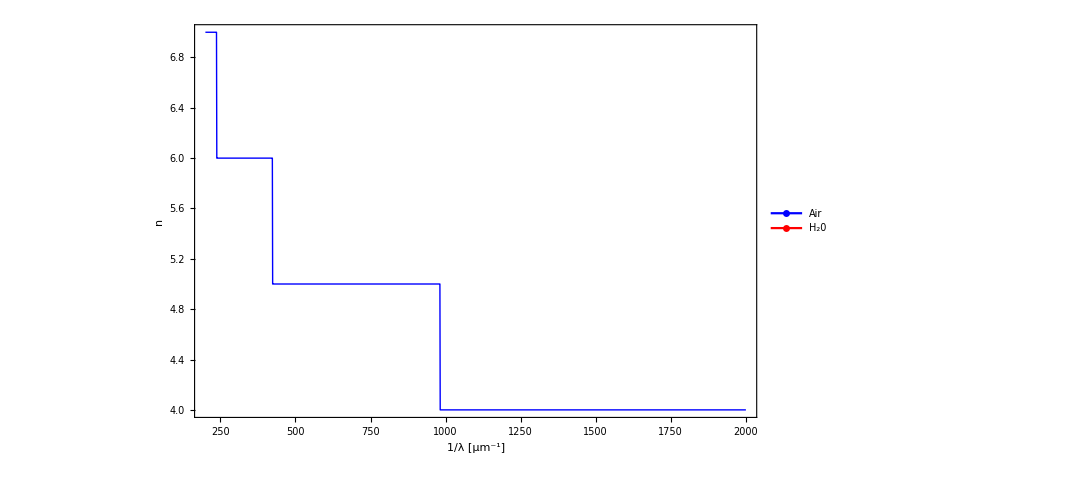

n_lambda.pdf

```mathematica
radio = 30(*nm*);
Table[{λ,Round[x+4 x^(1/3)+2]/.x-> 2π*#*radio/λ},{λ,200.,2000.}]&/@{1,nH2OFunc[λ]};
Show[ListLinePlot[%, PlotStyle->Table[{Thick,color[[i]]},{i,Length[color]}],
	PlotLegends->legendSquare[{"Air"," H_20"},"Row",{Left,Bottom}]],
		Frame-> True, PlotRange->All,
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["n",24,Bold],Null},{Style["1/λ [μm^-1]",24, Bold], Null}}, 
		ImageSize-> 800,
		Epilog->{Inset[Style["NP in air and H_2O", 24, Bold], {1250,45}],
			Inset[Style["Hale & Querry (1973) \n r = 1μm", 16], {1250,40}]}]
Export["n_lambda.pdf",%]
```

InterpolatingFunction::dmval: Input value {200.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {201.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {202.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

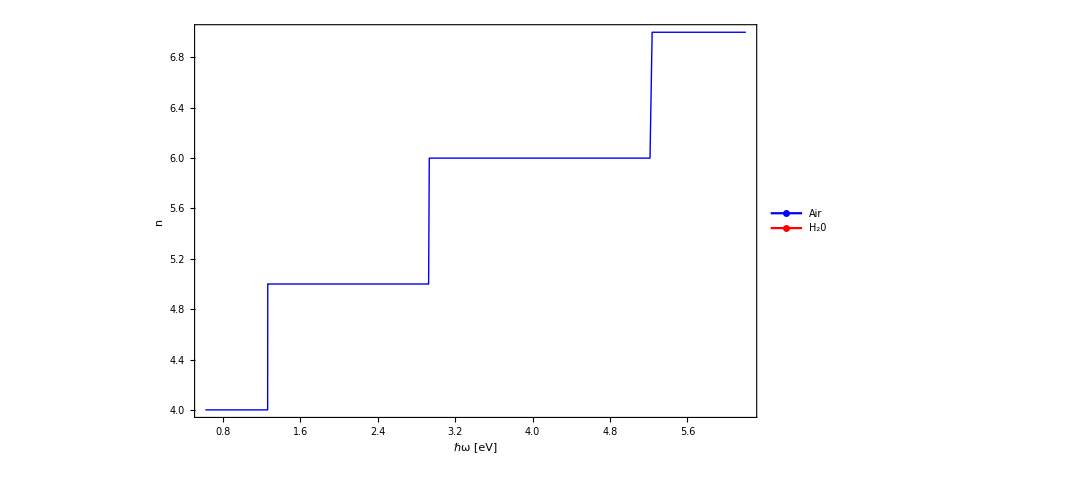

n_hw.pdf

```mathematica
Table[{h c/(λ),Round[x+4 x^(1/3)+2]/.x-> 2π*#*radio/λ},{λ,200.,2000.}]&/@{1,nH2OFunc[λ]};
Show[ListLinePlot[%, PlotStyle->Table[{Thick,color[[i]]},{i,Length[color]}],
	PlotLegends->legendSquare[{"Air"," H_20"},"Row",{Left,Bottom}]],
		Frame-> True, PlotRange->All,
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["n",24,Bold],Null},{Style["ℏω [eV]",24, Bold], Null}}, 
		ImageSize-> 800,
		Epilog->{Inset[Style["NP in air and H_2O", 24, Bold], {1.4,45}],
			Inset[Style["Hale & Querry (1973) \n r = 1μm", 16], {1.4,40}]}]
Export["n_hw.pdf",%]
```

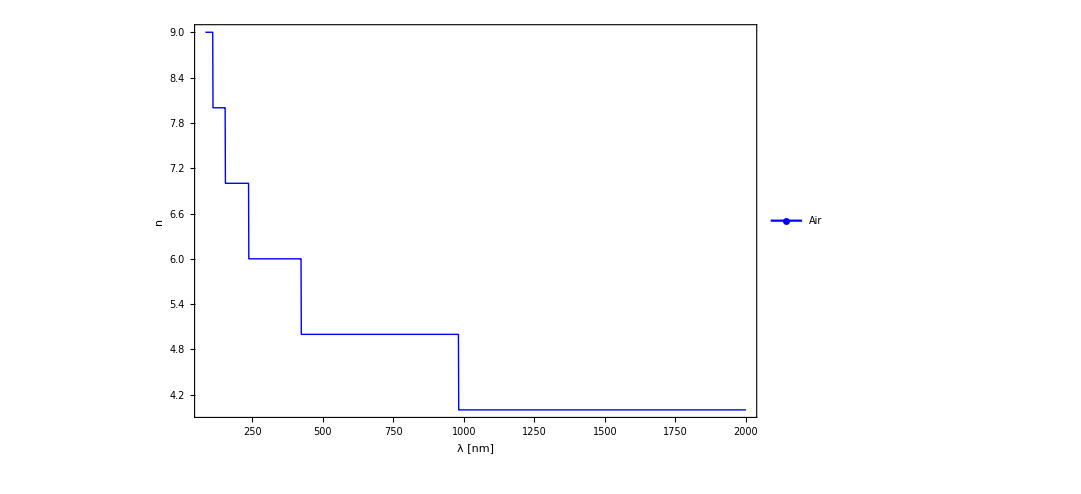

n_hw.pdf

```mathematica
Table[{λ,Round[x+4 x^(1/3)+2]/.x-> 2π*#*radio/λ},{λ,1.,2000.}]&/@{1};
Show[ListLinePlot[%, PlotStyle->Table[{Thick,color[[i]]},{i,Length[color]}],
	PlotLegends->legendSquare[{"Air"," H_20"},"Row",{Left,Bottom}]],
		Frame-> True, PlotRange->All,
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["n",24,Bold],Null},{Style["λ [nm]",24, Bold], Null}}, 
		ImageSize-> 800,
		Epilog->{Inset[Style["NP in air and H_2O", 24, Bold], {1000,100}],
			Inset[Style["Hale & Querry (1973) \n r = 1μm", 16], {1000,90}]}]
Export["n_hw.pdf",%]
```

```mathematica
If[(Round[x+4 x^(1/3)+2]/.x-> 2π*radio/500)> 15,a=15,a=Round[x+4 x^(1/3)+2]/.x-> 2π*radio/500]
a
```

5

5

### Q_sca & Q_ext with variable n

```mathematica
scaCQn[indexes_,λ_,rad_]:= Module[{an,bn,sum, nmax,x},
x = 2* π *indexes[[1]] *rad / λ;
nmax =  Round[x+4 x^(1/3)+2];
{an,bn} = mieCoef[Table[i,{i,nmax}],indexes,λ,rad];
sum = Sum[(2*i+1)* (Abs[an[[i]] ]^2+Abs[bn[[i]] ]^2),{i, Length[an]}];
sum = ((λ^2 )* sum)/(2*π*( Abs[indexes[[1]]]^2));
sum = sum / (π  *(rad^2))]
```

```mathematica
extCQn[indexes_,λ_,rad_]:= Module[{sum,an,bn,nmax,x},
x = 2* π *indexes[[1]] *rad / λ;
nmax =  Round[x+4 x^(1/3)+2];
{an,bn} = mieCoef[Table[i,{i,nmax}],indexes,λ,rad];
sum = Sum[(2*i+1)* Re[ an[[i]] + bn[[i]]  ],{i, Length[an]}];
sum = ((λ^2 )* sum)/(2*π*( Abs[indexes[[1]]]^2));
sum = sum / (π  *(rad^2))]
```

## Graphs with variable n

### Water droplet

```mathematica
color = {Blue, Red,Orange, Green, Purple, Pink}
(*orden = Table[i,{i,50,300,50}];*)
radio  = 1*^3  {1.,.75,.5,.25,.1}
```

{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0.5, 0],RGBColor[0, 1, 0],RGBColor[0.5, 0, 0.5],RGBColor[1, 0.5, 0.5]}

{1000.,750.,500.,250.,100.}

```mathematica
AbsoluteTiming[Table[{1000/(λ),extCQn[{1.,nH2OFunc[λ]},λ,#]},{λ,200.,2000.}]]&/@radio;
tiempo = %[[All,1]];
res = %%[[All,2]];
```

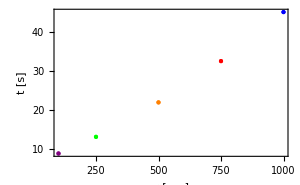
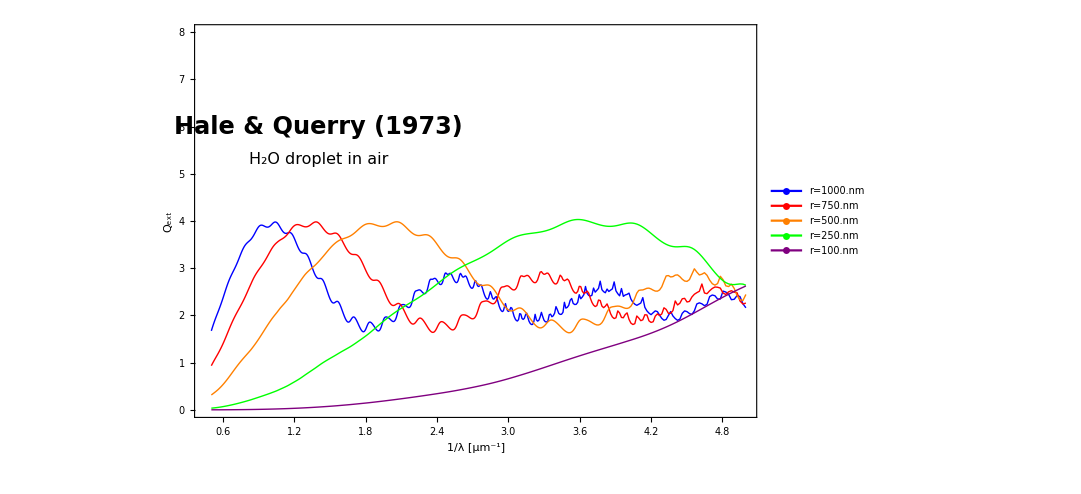

H2O_nVar_radii.pdf

```mathematica
Show[ListLinePlot[res, PlotStyle->Table[{Thick,color[[i]]},{i,Length[color]}],
	PlotLegends->legendSquare[Table["r="<>ToString[radio[[i]]]<>"nm",{i,Length[radio]}],"Row",{Left,Top}]],
		Frame-> True, PlotRange->{{.45,5},{0,8}},
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["Q_ext",24,Bold],Null},{Style["1/λ [μm^-1]",24, Bold], Null}}, 
		ImageSize-> 800,
		Epilog->{Inset[Style["Hale & Querry (1973)", 24, Bold], {1.4,6}],
			Inset[Style["H_2O droplet in air", 16], {1.4,5.3}]}];

Show[ListPlot[Table[{{radio[[i]],tiempo[[i]]}},{i,Length[tiempo]}],PlotStyle->Table[{PointSize[Large],color[[i]]},{i,Length[color]}]],
		Frame-> True,PlotRange-> All,
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["t [s]",24,Bold],Null},{Style["r [nm]",24, Bold], Null}}, 
		ImageSize-> 300];

Overlay[{%,%%},Alignment->{Right,Top}]
Export["H2O_nVar_radii.pdf",%]
```

### Au NP

```mathematica
color = {Blue, Red,Orange, Green, Purple, Pink}
```

{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0.5, 0],RGBColor[0, 1, 0],RGBColor[0.5, 0, 0.5],RGBColor[1, 0.5, 0.5]}

#### (variating r ) in air

```mathematica
radio  =  {1000,500,100,10} 
orden = 10
```

{1000,500,100,10}

10

```mathematica
AbsoluteTiming[Table[{h c/(λ),extCQn[{1.,nAuFunc[λ]},λ,#]},{λ,250.,1880.}]]&/@radio;
tiempo = %[[All,1]];
res = %%[[All,2]];
```

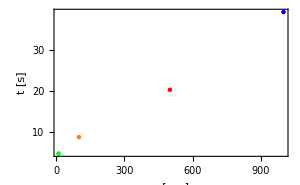
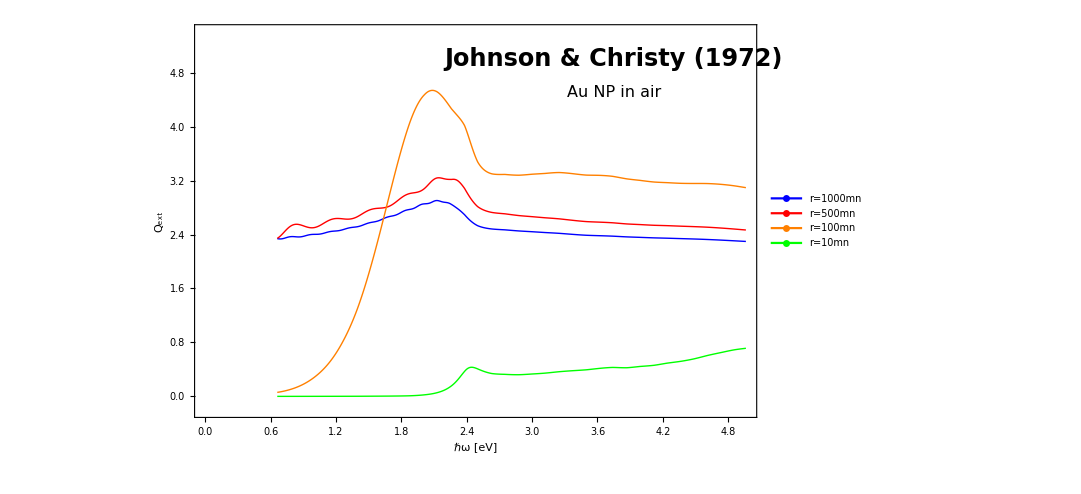

Au_nVar_radii.pdf

```mathematica
Show[ListLinePlot[res, PlotStyle->Table[{Thick,color[[i]]},{i,Length[color]}],PlotRange->{-.2,5.4},
	PlotLegends->legendSquare[Table["r="<>ToString[radio[[i]]]<>"mn",{i,Length[radio]}],"Row",{Right,Bottom}]],
		Frame-> True, 
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["Q_ext",24,Bold],Null},{Style["ℏω [eV]",24, Bold], Null}}, 
		ImageSize-> 800,
		Epilog->{Inset[Style["Johnson & Christy (1972)", 24, Bold], {3.75,5}],
			Inset[Style["Au NP in air", 16], {3.75,4.5}]}];

Show[ListPlot[Table[{{radio[[i]],tiempo[[i]]}},{i,Length[tiempo]}],PlotStyle->Table[{PointSize[Large],color[[i]]},{i,Length[color]}]],
		Frame-> True,PlotRange-> All,
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["t [s]",24,Bold],Null},{Style["r [nm]",24, Bold], Null}}, 
		ImageSize-> 300, ImagePadding-> {{100,5},{80,40}}];

Overlay[{%,%%},Alignment->{Left,Top}]
Export["Au_nVar_radii.pdf",%]
```

#### r=30nm in n_m=1

```mathematica
radio=30;
```

```mathematica
file = OpenAppend["AuNP_30nm_JC_Qext.csv", BinaryFormat->True];
WriteString[file,"lambda (nm), E(eV), Qext\n"];
Table[{λ,h c/(λ),extCQn[{1.,nAuFunc[λ]},λ,radio]},{λ,250.,1880.}];
Export[file, %];
Close["AuNP_30nm_JC_Qext.csv"];
```

```mathematica
FileNames["*.csv"]
data=Import[%[[1]],"Data"]
```

{AuNP_30nm_JC_Qext.csv}

{{lambda (nm),E(eV),Qext},{250.,4.9628,2.88128},{251.,4.94303,2.88234},{252.,4.92341,2.88322},{253.,4.90395,2.88376},{254.,4.88465,2.88378},{255.,4.86549,2.88309},{256.,4.84649,2.88065},{257.,4.82763,2.87686},{258.,4.80892,2.87206},{259.,4.79035,2.86628},{260.,4.77192,2.85954},{261.,4.75364,2.85188},{262.,4.7355,2.84345},{263.,4.71749,2.83455},{264.,4.69962,2.82485},{265.,4.68189,2.81434},{266.,4.66429,2.80302},{267.,4.64682,2.79088},{268.,4.62948,2.7779},{269.,4.61227,2.76407},{270.,4.59519,2.74841},{271.,4.57823,2.73184},{272.,4.5614,2.71463},{273.,4.54469,2.6969},{274.,4.5281,2.67878},{275.,4.51164,2.66038},{276.,4.49529,2.64184},{277.,4.47906,2.62375},{278.,4.46295,2.60596},{279.,4.44695,2.58829},{280.,4.43107,2.57077},{281.,4.4153,2.55343},{282.,4.39965,2.53632},{283.,4.3841,2.51945},{284.,4.36866,2.50285},{285.,4.35333,2.48697},{286.,4.33811,2.47192},{287.,4.323,2.45707},{288.,4.30799,2.44235},{289.,4.29308,2.42769},{290.,4.27828,2.41303},{291.,4.26357,2.3983},{292.,4.24897,2.38343},{293.,4.23447,2.3676},{294.,4.22007,2.35032},{295.,4.20576,2.33292},{296.,4.19155,2.31553},{297.,4.17744,2.29823},{298.,4.16342,2.28113},{299.,4.1495,2.26432},{300.,4.13567,2.24792},{301.,4.12193,2.232},{302.,4.10828,2.2187},{303.,4.09472,2.20632},{304.,4.08125,2.19446},{305.,4.06787,2.18304},{306.,4.05458,2.17199},{307.,4.04137,2.16125},{308.,4.02825,2.15073},{309.,4.01521,2.14037},{310.,4.00226,2.13009},{311.,3.98939,2.11971},{312.,3.9766,2.10708},{313.,3.9639,2.09449},{314.,3.95127,2.08202},{315.,3.93873,2.06973},{316.,3.92627,2.05771},{317.,3.91388,2.04603},{318.,3.90157,2.03476},{319.,3.88934,2.02398},{320.,3.87719,2.01376},{321.,3.86511,2.00554},{322.,3.85311,2.00001},{323.,3.84118,1.99514},{324.,3.82932,1.9908},{325.,3.81754,1.98689},{326.,3.80583,1.98332},{327.,3.79419,1.97996},{328.,3.78262,1.9767},{329.,3.77113,1.97343},{330.,3.7597,1.97002},{331.,3.74834,1.96636},{332.,3.73705,1.96149},{333.,3.72583,1.95383},{334.,3.71467,1.94573},{335.,3.70358,1.93722},{336.,3.69256,1.92833},{337.,3.6816,1.91911},{338.,3.67071,1.90958},{339.,3.65988,1.89979},{340.,3.64912,1.88976},{341.,3.63842,1.87955},{342.,3.62778,1.86917},{343.,3.6172,1.85866},{344.,3.60669,1.84799},{345.,3.59623,1.83727},{346.,3.58584,1.82656},{347.,3.5755,1.81587},{348.,3.56523,1.80525},{349.,3.55501,1.79474},{350.,3.54486,1.78437},{351.,3.53476,1.77417},{352.,3.52472,1.76418},{353.,3.51473,1.75444},{354.,3.5048,1.74497},{355.,3.49493,1.7366},{356.,3.48511,1.7293},{357.,3.47535,1.72231},{358.,3.46564,1.7156},{359.,3.45599,1.70913},{360.,3.44639,1.70289},{361.,3.43684,1.69686},{362.,3.42735,1.691},{363.,3.41791,1.68529},{364.,3.40852,1.67971},{365.,3.39918,1.67424},{366.,3.38989,1.66885},{367.,3.38065,1.66353},{368.,3.37147,1.65824},{369.,3.36233,1.65272},{370.,3.35324,1.64716},{371.,3.34421,1.6416},{372.,3.33522,1.63602},{373.,3.32627,1.63042},{374.,3.31738,1.62478},{375.,3.30853,1.6191},{376.,3.29973,1.61337},{377.,3.29098,1.60758},{378.,3.28228,1.60172},{379.,3.27362,1.59579},{380.,3.265,1.58977},{381.,3.25643,1.58367},{382.,3.24791,1.57726},{383.,3.23943,1.57013},{384.,3.23099,1.56292},{385.,3.2226,1.55564},{386.,3.21425,1.54832},{387.,3.20594,1.54096},{388.,3.19768,1.53358},{389.,3.18946,1.52621},{390.,3.18128,1.51884},{391.,3.17315,1.51151},{392.,3.16505,1.50422},{393.,3.157,1.49698},{394.,3.14899,1.48982},{395.,3.14101,1.48274},{396.,3.13308,1.47576},{397.,3.12519,1.46889},{398.,3.11734,1.46239},{399.,3.10952,1.45652},{400.,3.10175,1.45076},{401.,3.09402,1.44511},{402.,3.08632,1.43957},{403.,3.07866,1.43413},{404.,3.07104,1.42878},{405.,3.06346,1.42353},{406.,3.05591,1.41836},{407.,3.0484,1.41328},{408.,3.04093,1.40827},{409.,3.0335,1.40333},{410.,3.0261,1.39846},{411.,3.01874,1.39365},{412.,3.01141,1.38891},{413.,3.00412,1.38421},{414.,2.99686,1.37932},{415.,2.98964,1.37416},{416.,2.98245,1.36905},{417.,2.9753,1.364},{418.,2.96818,1.35903},{419.,2.9611,1.35413},{420.,2.95405,1.34932},{421.,2.94703,1.3446},{422.,2.94005,1.33997},{423.,2.9331,1.33546},{424.,2.92618,1.33105},{425.,2.91929,1.32677},{426.,2.91244,1.32262},{427.,2.90562,1.3186},{428.,2.89883,1.31472},{429.,2.89208,1.31099},{430.,2.88535,1.30742},{431.,2.87865,1.30418},{432.,2.87199,1.30179},{433.,2.86536,1.29957},{434.,2.85876,1.29752},{435.,2.85218,1.29564},{436.,2.84564,1.29391},{437.,2.83913,1.29234},{438.,2.83265,1.29091},{439.,2.8262,1.28962},{440.,2.81977,1.28846},{441.,2.81338,1.28742},{442.,2.80701,1.28651},{443.,2.80068,1.2857},{444.,2.79437,1.28501},{445.,2.78809,1.28442},{446.,2.78184,1.28392},{447.,2.77562,1.28351},{448.,2.76942,1.28318},{449.,2.76325,1.28293},{450.,2.75711,1.28274},{451.,2.751,1.28262},{452.,2.74491,1.28142},{453.,2.73885,1.28006},{454.,2.73282,1.27876},{455.,2.72681,1.27754},{456.,2.72083,1.27641},{457.,2.71488,1.27538},{458.,2.70895,1.27446},{459.,2.70305,1.27368},{460.,2.69717,1.27303},{461.,2.69132,1.27254},{462.,2.6855,1.27222},{463.,2.6797,1.27208},{464.,2.67392,1.27214},{465.,2.66817,1.27241},{466.,2.66245,1.27291},{467.,2.65675,1.27365},{468.,2.65107,1.27465},{469.,2.64542,1.27593},{470.,2.63979,1.27751},{471.,2.63418,1.2794},{472.,2.6286,1.28207},{473.,2.62304,1.28647},{474.,2.61751,1.29127},{475.,2.612,1.29648},{476.,2.60651,1.3021},{477.,2.60105,1.30813},{478.,2.59561,1.31458},{479.,2.59019,1.32143},{480.,2.58479,1.32871},{481.,2.57942,1.3364},{482.,2.57407,1.34452},{483.,2.56874,1.35305},{484.,2.56343,1.36201},{485.,2.55814,1.37138},{486.,2.55288,1.38117},{487.,2.54764,1.39137},{488.,2.54242,1.40198},{489.,2.53722,1.41299},{490.,2.53204,1.42439},{491.,2.52688,1.43617},{492.,2.52175,1.44831},{493.,2.51663,1.46079},{494.,2.51154,1.47359},{495.,2.50647,1.48668},{496.,2.50141,1.50001},{497.,2.49638,1.51441},{498.,2.49137,1.52918},{499.,2.48637,1.54386},{500.,2.4814,1.55835},{501.,2.47645,1.57253},{502.,2.47151,1.58627},{503.,2.4666,1.59944},{504.,2.46171,1.61187},{505.,2.45683,1.62342},{506.,2.45198,1.63392},{507.,2.44714,1.64319},{508.,2.44232,1.65104},{509.,2.43752,1.6573},{510.,2.43275,1.66179},{511.,2.42798,1.66431},{512.,2.42324,1.66471},{513.,2.41852,1.66282},{514.,2.41381,1.65849},{515.,2.40913,1.6516},{516.,2.40446,1.64206},{517.,2.39981,1.62979},{518.,2.39517,1.61477},{519.,2.39056,1.59699},{520.,2.38596,1.5765},{521.,2.38138,1.55339},{522.,2.37682,1.5273},{523.,2.37228,1.49934},{524.,2.36775,1.47001},{525.,2.36324,1.43951},{526.,2.35875,1.40803},{527.,2.35427,1.37576},{528.,2.34981,1.34288},{529.,2.34537,1.30957},{530.,2.34094,1.276},{531.,2.33654,1.24232},{532.,2.33214,1.20868},{533.,2.32777,1.17521},{534.,2.32341,1.14204},{535.,2.31907,1.10925},{536.,2.31474,1.07696},{537.,2.31043,1.04523},{538.,2.30613,1.01413},{539.,2.30186,0.983727},{540.,2.29759,0.954058},{541.,2.29335,0.92516},{542.,2.28911,0.897059},{543.,2.2849,0.869773},{544.,2.2807,0.843312},{545.,2.27651,0.817681},{546.,2.27234,0.792878},{547.,2.26819,0.768898},{548.,2.26405,0.74573},{549.,2.25993,0.723364},{550.,2.25582,0.701937},{551.,2.25172,0.681171},{552.,2.24765,0.661054},{553.,2.24358,0.641573},{554.,2.23953,0.622715},{555.,2.2355,0.604465},{556.,2.23148,0.586808},{557.,2.22747,0.569729},{558.,2.22348,0.553212},{559.,2.2195,0.537242},{560.,2.21554,0.521803},{561.,2.21159,0.506879},{562.,2.20765,0.492455},{563.,2.20373,0.478514},{564.,2.19982,0.465042},{565.,2.19593,0.452024},{566.,2.19205,0.439444},{567.,2.18818,0.427287},{568.,2.18433,0.41554},{569.,2.18049,0.404188},{570.,2.17667,0.393218},{571.,2.17285,0.382616},{572.,2.16906,0.372369},{573.,2.16527,0.362465},{574.,2.1615,0.352892},{575.,2.15774,0.343637},{576.,2.15399,0.334689},{577.,2.15026,0.326037},{578.,2.14654,0.317671},{579.,2.14283,0.309579},{580.,2.13914,0.301752},{581.,2.13546,0.294179},{582.,2.13179,0.286853},{583.,2.12813,0.279698},{584.,2.12449,0.272716},{585.,2.12086,0.265962},{586.,2.11724,0.259429},{587.,2.11363,0.253108},{588.,2.11003,0.246991},{589.,2.10645,0.241073},{590.,2.10288,0.235345},{591.,2.09932,0.2298},{592.,2.09578,0.224432},{593.,2.09224,0.219235},{594.,2.08872,0.214203},{595.,2.08521,0.209329},{596.,2.08171,0.204607},{597.,2.07822,0.200033},{598.,2.07475,0.195601},{599.,2.07129,0.191305},{600.,2.06783,0.187141},{601.,2.06439,0.183104},{602.,2.06096,0.179189},{603.,2.05755,0.175393},{604.,2.05414,0.171709},{605.,2.05074,0.168135},{606.,2.04736,0.164667},{607.,2.04399,0.1613},{608.,2.04063,0.158031},{609.,2.03727,0.154856},{610.,2.03393,0.151773},{611.,2.03061,0.148777},{612.,2.02729,0.145865},{613.,2.02398,0.143035},{614.,2.02068,0.140283},{615.,2.0174,0.137608},{616.,2.01412,0.135005},{617.,2.01086,0.132472},{618.,2.00761,0.129943},{619.,2.00436,0.127457},{620.,2.00113,0.125035},{621.,1.99791,0.122674},{622.,1.99469,0.120374},{623.,1.99149,0.118132},{624.,1.9883,0.115946},{625.,1.98512,0.113816},{626.,1.98195,0.111739},{627.,1.97879,0.109713},{628.,1.97564,0.107738},{629.,1.9725,0.105813},{630.,1.96937,0.103934},{631.,1.96624,0.102103},{632.,1.96313,0.100316},{633.,1.96003,0.0985734},{634.,1.95694,0.0968734},{635.,1.95386,0.095215},{636.,1.95079,0.0935972},{637.,1.94772,0.0920188},{638.,1.94467,0.0904788},{639.,1.94163,0.0889763},{640.,1.93859,0.0875104},{641.,1.93557,0.08608},{642.,1.93255,0.0846843},{643.,1.92955,0.0833224},{644.,1.92655,0.0819935},{645.,1.92357,0.0806968},{646.,1.92059,0.0794315},{647.,1.91762,0.0781969},{648.,1.91466,0.0769922},{649.,1.91171,0.0758167},{650.,1.90877,0.0746697},{651.,1.90584,0.0735506},{652.,1.90291,0.0724587},{653.,1.9,0.0713933},{654.,1.8971,0.070354},{655.,1.8942,0.06934},{656.,1.89131,0.0683508},{657.,1.88843,0.0673859},{658.,1.88556,0.0664446},{659.,1.8827,0.0655266},{660.,1.87985,0.0646345},{661.,1.877,0.0638214},{662.,1.87417,0.0630287},{663.,1.87134,0.062256},{664.,1.86852,0.0615026},{665.,1.86571,0.0607678},{666.,1.86291,0.0600512},{667.,1.86012,0.0593521},{668.,1.85734,0.0586701},{669.,1.85456,0.0580045},{670.,1.85179,0.057355},{671.,1.84903,0.056721},{672.,1.84628,0.056102},{673.,1.84354,0.0554976},{674.,1.8408,0.0549073},{675.,1.83807,0.0543308},{676.,1.83536,0.0537675},{677.,1.83264,0.0532171},{678.,1.82994,0.0526791},{679.,1.82725,0.0521532},{680.,1.82456,0.0516391},{681.,1.82188,0.0511363},{682.,1.81921,0.0506445},{683.,1.81654,0.0501634},{684.,1.81389,0.0496927},{685.,1.81124,0.0492319},{686.,1.8086,0.0487808},{687.,1.80597,0.0483392},{688.,1.80334,0.0479066},{689.,1.80073,0.0474828},{690.,1.79812,0.0470676},{691.,1.79551,0.0466607},{692.,1.79292,0.0462618},{693.,1.79033,0.0458706},{694.,1.78775,0.0454869},{695.,1.78518,0.0451105},{696.,1.78262,0.0447412},{697.,1.78006,0.0443786},{698.,1.77751,0.0440226},{699.,1.77496,0.043673},{700.,1.77243,0.0433296},{701.,1.7699,0.0429921},{702.,1.76738,0.0426604},{703.,1.76487,0.0423343},{704.,1.76236,0.0420135},{705.,1.75986,0.0416967},{706.,1.75737,0.041363},{707.,1.75488,0.0410345},{708.,1.7524,0.0407111},{709.,1.74993,0.0403926},{710.,1.74747,0.040079},{711.,1.74501,0.0397702},{712.,1.74256,0.039466},{713.,1.74011,0.0391663},{714.,1.73768,0.0388711},{715.,1.73525,0.0385803},{716.,1.73282,0.0382937},{717.,1.7304,0.0380113},{718.,1.72799,0.0377329},{719.,1.72559,0.0374586},{720.,1.72319,0.0371881},{721.,1.7208,0.0369215},{722.,1.71842,0.0366586},{723.,1.71604,0.0363994},{724.,1.71367,0.0361438},{725.,1.71131,0.0358917},{726.,1.70895,0.035643},{727.,1.7066,0.0353977},{728.,1.70426,0.0351556},{729.,1.70192,0.0349168},{730.,1.69959,0.0346811},{731.,1.69726,0.0344486},{732.,1.69495,0.034219},{733.,1.69263,0.0339924},{734.,1.69033,0.0337687},{735.,1.68803,0.0335478},{736.,1.68573,0.0333297},{737.,1.68345,0.0331144},{738.,1.68117,0.0329016},{739.,1.67889,0.0326915},{740.,1.67662,0.032484},{741.,1.67436,0.0322789},{742.,1.6721,0.0320763},{743.,1.66985,0.031876},{744.,1.66761,0.0316782},{745.,1.66537,0.0314826},{746.,1.66314,0.0312892},{747.,1.66091,0.0310981},{748.,1.65869,0.0309091},{749.,1.65648,0.0307222},{750.,1.65427,0.0305374},{751.,1.65206,0.0303546},{752.,1.64987,0.0301738},{753.,1.64768,0.029995},{754.,1.64549,0.029818},{755.,1.64331,0.0296429},{756.,1.64114,0.0294696},{757.,1.63897,0.0292964},{758.,1.63681,0.0291229},{759.,1.63465,0.0289512},{760.,1.6325,0.0287813},{761.,1.63036,0.028613},{762.,1.62822,0.0284464},{763.,1.62608,0.0282814},{764.,1.62395,0.028118},{765.,1.62183,0.0279562},{766.,1.61971,0.027796},{767.,1.6176,0.0276373},{768.,1.6155,0.02748},{769.,1.61339,0.0273243},{770.,1.6113,0.02717},{771.,1.60921,0.0270171},{772.,1.60712,0.0268656},{773.,1.60505,0.0267155},{774.,1.60297,0.0265668},{775.,1.6009,0.0264194},{776.,1.59884,0.0262733},{777.,1.59678,0.0261285},{778.,1.59473,0.025985},{779.,1.59268,0.0258427},{780.,1.59064,0.0257017},{781.,1.5886,0.0255619},{782.,1.58657,0.0254232},{783.,1.58455,0.0252858},{784.,1.58253,0.0251494},{785.,1.58051,0.0250142},{786.,1.5785,0.0248802},{787.,1.57649,0.0247472},{788.,1.57449,0.0246153},{789.,1.5725,0.0244845},{790.,1.57051,0.0243547},{791.,1.56852,0.0242259},{792.,1.56654,0.0240982},{793.,1.56457,0.0239714},{794.,1.56259,0.0238456},{795.,1.56063,0.0237208},{796.,1.55867,0.023597},{797.,1.55671,0.023474},{798.,1.55476,0.023352},{799.,1.55282,0.0232309},{800.,1.55088,0.0231107},{801.,1.54894,0.0229914},{802.,1.54701,0.0228729},{803.,1.54508,0.0227553},{804.,1.54316,0.0226385},{805.,1.54124,0.0225225},{806.,1.53933,0.0224074},{807.,1.53742,0.022293},{808.,1.53552,0.0221794},{809.,1.53362,0.0220666},{810.,1.53173,0.0219546},{811.,1.52984,0.0218433},{812.,1.52796,0.0217327},{813.,1.52608,0.0216229},{814.,1.5242,0.0215138},{815.,1.52233,0.0214053},{816.,1.52047,0.0212976},{817.,1.5186,0.0211906},{818.,1.51675,0.0210842},{819.,1.5149,0.0209785},{820.,1.51305,0.0208734},{821.,1.51121,0.020769},{822.,1.50937,0.0206621},{823.,1.50753,0.0205499},{824.,1.5057,0.0204385},{825.,1.50388,0.0203278},{826.,1.50206,0.0202177},{827.,1.50024,0.0201084},{828.,1.49843,0.0199998},{829.,1.49662,0.019892},{830.,1.49482,0.0197848},{831.,1.49302,0.0196784},{832.,1.49123,0.0195727},{833.,1.48944,0.0194677},{834.,1.48765,0.0193634},{835.,1.48587,0.0192599},{836.,1.48409,0.019157},{837.,1.48232,0.0190549},{838.,1.48055,0.0189535},{839.,1.47878,0.0188528},{840.,1.47702,0.0187528},{841.,1.47527,0.0186536},{842.,1.47352,0.018555},{843.,1.47177,0.0184572},{844.,1.47002,0.0183601},{845.,1.46828,0.0182637},{846.,1.46655,0.018168},{847.,1.46482,0.0180731},{848.,1.46309,0.0179788},{849.,1.46137,0.0178853},{850.,1.45965,0.0177924},{851.,1.45793,0.0177003},{852.,1.45622,0.0176089},{853.,1.45451,0.0175181},{854.,1.45281,0.0174281},{855.,1.45111,0.0173388},{856.,1.44942,0.0172502},{857.,1.44772,0.0171623},{858.,1.44604,0.0170751},{859.,1.44435,0.0169886},{860.,1.44267,0.0169028},{861.,1.441,0.0168176},{862.,1.43933,0.0167332},{863.,1.43766,0.0166495},{864.,1.436,0.0165664},{865.,1.43434,0.0164841},{866.,1.43268,0.0164024},{867.,1.43103,0.0163214},{868.,1.42938,0.0162411},{869.,1.42773,0.0161615},{870.,1.42609,0.0160825},{871.,1.42445,0.0160043},{872.,1.42282,0.0159267},{873.,1.42119,0.0158498},{874.,1.41957,0.0157735},{875.,1.41794,0.0156979},{876.,1.41632,0.015623},{877.,1.41471,0.0155488},{878.,1.4131,0.0154752},{879.,1.41149,0.0154023},{880.,1.40989,0.0153301},{881.,1.40829,0.0152585},{882.,1.40669,0.0151875},{883.,1.4051,0.0151172},{884.,1.40351,0.0150476},{885.,1.40192,0.0149786},{886.,1.40034,0.0149103},{887.,1.39876,0.0148426},{888.,1.39718,0.0147755},{889.,1.39561,0.0147091},{890.,1.39405,0.0146434},{891.,1.39248,0.0145782},{892.,1.39092,0.0145137},{893.,1.38936,0.0144534},{894.,1.38781,0.0143988},{895.,1.38626,0.0143448},{896.,1.38471,0.0142914},{897.,1.38317,0.0142385},{898.,1.38163,0.0141862},{899.,1.38009,0.0141344},{900.,1.37856,0.0140832},{901.,1.37703,0.0140325},{902.,1.3755,0.0139823},{903.,1.37398,0.0139327},{904.,1.37246,0.0138835},{905.,1.37094,0.0138348},{906.,1.36943,0.0137867},{907.,1.36792,0.013739},{908.,1.36641,0.0136918},{909.,1.36491,0.013645},{910.,1.36341,0.0135987},{911.,1.36191,0.0135529},{912.,1.36042,0.0135075},{913.,1.35893,0.0134625},{914.,1.35744,0.013418},{915.,1.35596,0.0133738},{916.,1.35448,0.0133301},{917.,1.353,0.0132868},{918.,1.35153,0.0132439},{919.,1.35005,0.0132014},{920.,1.34859,0.0131593},{921.,1.34712,0.0131175},{922.,1.34566,0.0130762},{923.,1.3442,0.0130351},{924.,1.34275,0.0129945},{925.,1.3413,0.0129542},{926.,1.33985,0.0129143},{927.,1.3384,0.0128746},{928.,1.33696,0.0128354},{929.,1.33552,0.0127964},{930.,1.33409,0.0127578},{931.,1.33265,0.0127195},{932.,1.33122,0.0126815},{933.,1.3298,0.0126438},{934.,1.32837,0.0126064},{935.,1.32695,0.0125693},{936.,1.32553,0.0125326},{937.,1.32412,0.012496},{938.,1.32271,0.0124598},{939.,1.3213,0.0124239},{940.,1.31989,0.0123882},{941.,1.31849,0.0123527},{942.,1.31709,0.0123176},{943.,1.31569,0.0122827},{944.,1.3143,0.012248},{945.,1.31291,0.0122136},{946.,1.31152,0.0121794},{947.,1.31014,0.0121455},{948.,1.30876,0.0121118},{949.,1.30738,0.0120783},{950.,1.306,0.0120451},{951.,1.30463,0.012012},{952.,1.30326,0.0119792},{953.,1.30189,0.0119466},{954.,1.30052,0.0119142},{955.,1.29916,0.011882},{956.,1.2978,0.01185},{957.,1.29645,0.0118182},{958.,1.29509,0.0117866},{959.,1.29374,0.0117552},{960.,1.2924,0.0117239},{961.,1.29105,0.0116929},{962.,1.28971,0.011662},{963.,1.28837,0.0116313},{964.,1.28703,0.0116007},{965.,1.2857,0.0115703},{966.,1.28437,0.0115401},{967.,1.28304,0.0115101},{968.,1.28172,0.0114802},{969.,1.28039,0.0114504},{970.,1.27907,0.0114208},{971.,1.27776,0.0113913},{972.,1.27644,0.011362},{973.,1.27513,0.0113328},{974.,1.27382,0.0113037},{975.,1.27251,0.0112748},{976.,1.27121,0.011246},{977.,1.26991,0.0112174},{978.,1.26861,0.0111888},{979.,1.26731,0.0111604},{980.,1.26602,0.0111321},{981.,1.26473,0.0111039},{982.,1.26344,0.0110758},{983.,1.26216,0.0110479},{984.,1.26087,0.01102},{985.,1.25959,0.0109908},{986.,1.25832,0.0109588},{987.,1.25704,0.010927},{988.,1.25577,0.0108952},{989.,1.2545,0.0108636},{990.,1.25323,0.0108321},{991.,1.25197,0.0108007},{992.,1.25071,0.0107695},{993.,1.24945,0.0107384},{994.,1.24819,0.0107074},{995.,1.24693,0.0106765},{996.,1.24568,0.0106458},{997.,1.24443,0.0106152},{998.,1.24319,0.0105847},{999.,1.24194,0.0105543},{1000.,1.2407,0.0105241},{1001.,1.23946,0.010494},{1002.,1.23822,0.010464},{1003.,1.23699,0.0104341},{1004.,1.23576,0.0104044},{1005.,1.23453,0.0103748},{1006.,1.2333,0.0103453},{1007.,1.23208,0.0103159},{1008.,1.23085,0.0102867},{1009.,1.22963,0.0102575},{1010.,1.22842,0.0102286},{1011.,1.2272,0.0101997},{1012.,1.22599,0.0101709},{1013.,1.22478,0.0101423},{1014.,1.22357,0.0101138},{1015.,1.22236,0.0100854},{1016.,1.22116,0.0100572},{1017.,1.21996,0.0100291},{1018.,1.21876,0.010001},{1019.,1.21757,0.00997316},{1020.,1.21637,0.0099454},{1021.,1.21518,0.00991775},{1022.,1.21399,0.00989023},{1023.,1.21281,0.00986283},{1024.,1.21162,0.00983556},{1025.,1.21044,0.0098084},{1026.,1.20926,0.00978136},{1027.,1.20808,0.00975445},{1028.,1.20691,0.00972765},{1029.,1.20573,0.00970097},{1030.,1.20456,0.00967442},{1031.,1.20339,0.00964798},{1032.,1.20223,0.00962167},{1033.,1.20107,0.00959547},{1034.,1.1999,0.00956939},{1035.,1.19874,0.00954343},{1036.,1.19759,0.00951759},{1037.,1.19643,0.00949187},{1038.,1.19528,0.00946626},{1039.,1.19413,0.00944077},{1040.,1.19298,0.0094154},{1041.,1.19183,0.00939015},{1042.,1.19069,0.00936502},{1043.,1.18955,0.00934},{1044.,1.18841,0.0093151},{1045.,1.18727,0.00929031},{1046.,1.18614,0.00926564},{1047.,1.185,0.00924109},{1048.,1.18387,0.00921665},{1049.,1.18275,0.00919232},{1050.,1.18162,0.00916812},{1051.,1.18049,0.00914402},{1052.,1.17937,0.00912004},{1053.,1.17825,0.00909618},{1054.,1.17713,0.00907243},{1055.,1.17602,0.00904879},{1056.,1.17491,0.00902527},{1057.,1.17379,0.00900185},{1058.,1.17268,0.00897856},{1059.,1.17158,0.00895537},{1060.,1.17047,0.0089323},{1061.,1.16937,0.00890934},{1062.,1.16827,0.00888649},{1063.,1.16717,0.00886375},{1064.,1.16607,0.00884112},{1065.,1.16498,0.00881861},{1066.,1.16388,0.0087962},{1067.,1.16279,0.00877391},{1068.,1.1617,0.00875172},{1069.,1.16062,0.00872965},{1070.,1.15953,0.00870769},{1071.,1.15845,0.00868583},{1072.,1.15737,0.00866408},{1073.,1.15629,0.00864244},{1074.,1.15521,0.00862091},{1075.,1.15414,0.00859949},{1076.,1.15307,0.00857818},{1077.,1.152,0.00855697},{1078.,1.15093,0.00853587},{1079.,1.14986,0.00851488},{1080.,1.1488,0.008494},{1081.,1.14773,0.00847322},{1082.,1.14667,0.00845255},{1083.,1.14561,0.00843198},{1084.,1.14456,0.00841152},{1085.,1.1435,0.00839116},{1086.,1.14245,0.00837091},{1087.,1.1414,0.00835076},{1088.,1.14035,0.00833072},{1089.,1.1393,0.00831185},{1090.,1.13826,0.00829361},{1091.,1.13721,0.00827547},{1092.,1.13617,0.00825742},{1093.,1.13513,0.00823947},{1094.,1.1341,0.00822161},{1095.,1.13306,0.00820385},{1096.,1.13203,0.00818618},{1097.,1.13099,0.0081686},{1098.,1.12996,0.00815111},{1099.,1.12894,0.00813371},{1100.,1.12791,0.0081164},{1101.,1.12688,0.00809918},{1102.,1.12586,0.00808204},{1103.,1.12484,0.00806499},{1104.,1.12382,0.00804803},{1105.,1.12281,0.00803115},{1106.,1.12179,0.00801435},{1107.,1.12078,0.00799764},{1108.,1.11977,0.00798101},{1109.,1.11876,0.00796446},{1110.,1.11775,0.00794799},{1111.,1.11674,0.0079316},{1112.,1.11574,0.00791528},{1113.,1.11474,0.00789905},{1114.,1.11373,0.00788289},{1115.,1.11274,0.00786681},{1116.,1.11174,0.00785081},{1117.,1.11074,0.00783488},{1118.,1.10975,0.00781902},{1119.,1.10876,0.00780324},{1120.,1.10777,0.00778753},{1121.,1.10678,0.00777189},{1122.,1.10579,0.00775632},{1123.,1.10481,0.00774082},{1124.,1.10383,0.00772539},{1125.,1.10284,0.00771004},{1126.,1.10187,0.00769474},{1127.,1.10089,0.00767952},{1128.,1.09991,0.00766437},{1129.,1.09894,0.00764928},{1130.,1.09796,0.00763425},{1131.,1.09699,0.00761929},{1132.,1.09602,0.0076044},{1133.,1.09506,0.00758957},{1134.,1.09409,0.0075748},{1135.,1.09313,0.00756009},{1136.,1.09217,0.00754545},{1137.,1.09121,0.00753086},{1138.,1.09025,0.00751634},{1139.,1.08929,0.00750188},{1140.,1.08833,0.00748748},{1141.,1.08738,0.00747313},{1142.,1.08643,0.00745884},{1143.,1.08548,0.00744461},{1144.,1.08453,0.00743044},{1145.,1.08358,0.00741632},{1146.,1.08264,0.00740226},{1147.,1.08169,0.00738826},{1148.,1.08075,0.00737431},{1149.,1.07981,0.00736041},{1150.,1.07887,0.00734656},{1151.,1.07793,0.00733277},{1152.,1.077,0.00731903},{1153.,1.07606,0.00730535},{1154.,1.07513,0.00729171},{1155.,1.0742,0.00727813},{1156.,1.07327,0.00726459},{1157.,1.07234,0.00725111},{1158.,1.07142,0.00723767},{1159.,1.07049,0.00722428},{1160.,1.06957,0.00721095},{1161.,1.06865,0.00719765},{1162.,1.06773,0.00718441},{1163.,1.06681,0.00717121},{1164.,1.06589,0.00715806},{1165.,1.06498,0.00714496},{1166.,1.06407,0.0071319},{1167.,1.06315,0.00711888},{1168.,1.06224,0.00710591},{1169.,1.06133,0.00709298},{1170.,1.06043,0.0070801},{1171.,1.05952,0.00706726},{1172.,1.05862,0.00705446},{1173.,1.05772,0.0070417},{1174.,1.05681,0.00702899},{1175.,1.05592,0.00701631},{1176.,1.05502,0.00700368},{1177.,1.05412,0.00699109},{1178.,1.05323,0.00697854},{1179.,1.05233,0.00696602},{1180.,1.05144,0.00695355},{1181.,1.05055,0.00694111},{1182.,1.04966,0.00692872},{1183.,1.04877,0.00691636},{1184.,1.04789,0.00690403},{1185.,1.047,0.00689175},{1186.,1.04612,0.0068795},{1187.,1.04524,0.00686729},{1188.,1.04436,0.00685511},{1189.,1.04348,0.00684297},{1190.,1.04261,0.00683086},{1191.,1.04173,0.00681879},{1192.,1.04086,0.00680675},{1193.,1.03998,0.00679475},{1194.,1.03911,0.00678278},{1195.,1.03824,0.00677084},{1196.,1.03737,0.00675894},{1197.,1.03651,0.00674707},{1198.,1.03564,0.00673523},{1199.,1.03478,0.00672342},{1200.,1.03392,0.00671164},{1201.,1.03306,0.0066999},{1202.,1.0322,0.00668818},{1203.,1.03134,0.0066765},{1204.,1.03048,0.00666485},{1205.,1.02963,0.00665322},{1206.,1.02877,0.00664163},{1207.,1.02792,0.00663006},{1208.,1.02707,0.00661852},{1209.,1.02622,0.00660701},{1210.,1.02537,0.00659553},{1211.,1.02453,0.00658408},{1212.,1.02368,0.00657266},{1213.,1.02284,0.00656126},{1214.,1.02199,0.00654988},{1215.,1.02115,0.00653854},{1216.,1.02031,0.00652722},{1217.,1.01947,0.00651503},{1218.,1.01864,0.00650234},{1219.,1.0178,0.00648967},{1220.,1.01697,0.00647704},{1221.,1.01613,0.00646443},{1222.,1.0153,0.00645184},{1223.,1.01447,0.00643929},{1224.,1.01364,0.00642676},{1225.,1.01282,0.00641427},{1226.,1.01199,0.0064018},{1227.,1.01117,0.00638936},{1228.,1.01034,0.00637694},{1229.,1.00952,0.00636456},{1230.,1.0087,0.0063522},{1231.,1.00788,0.00633988},{1232.,1.00706,0.00632758},{1233.,1.00625,0.00631531},{1234.,1.00543,0.00630307},{1235.,1.00462,0.00629086},{1236.,1.0038,0.00627867},{1237.,1.00299,0.00626652},{1238.,1.00218,0.00625439},{1239.,1.00137,0.0062423},{1240.,1.00056,0.00623023},{1241.,0.999758,0.00621819},{1242.,0.998953,0.00620619},{1243.,0.99815,0.00619421},{1244.,0.997347,0.00618226},{1245.,0.996546,0.00617033},{1246.,0.995747,0.00615844},{1247.,0.994948,0.00614658},{1248.,0.994151,0.00613475},{1249.,0.993355,0.00612294},{1250.,0.99256,0.00611117},{1251.,0.991767,0.00609943},{1252.,0.990975,0.00608771},{1253.,0.990184,0.00607603},{1254.,0.989394,0.00606437},{1255.,0.988606,0.00605274},{1256.,0.987819,0.00604115},{1257.,0.987033,0.00602958},{1258.,0.986248,0.00601804},{1259.,0.985465,0.00600654},{1260.,0.984683,0.00599506},{1261.,0.983902,0.00598361},{1262.,0.983122,0.0059722},{1263.,0.982344,0.00596081},{1264.,0.981567,0.00594945},{1265.,0.980791,0.00593812},{1266.,0.980016,0.00592682},{1267.,0.979242,0.00591556},{1268.,0.97847,0.00590432},{1269.,0.977699,0.00589311},{1270.,0.976929,0.00588193},{1271.,0.976161,0.00587078},{1272.,0.975393,0.00585966},{1273.,0.974627,0.00584858},{1274.,0.973862,0.00583752},{1275.,0.973098,0.00582649},{1276.,0.972336,0.00581549},{1277.,0.971574,0.00580453},{1278.,0.970814,0.00579359},{1279.,0.970055,0.00578268},{1280.,0.969297,0.0057718},{1281.,0.96854,0.00576095},{1282.,0.967785,0.00575014},{1283.,0.967031,0.00573935},{1284.,0.966277,0.00572859},{1285.,0.965525,0.00571787},{1286.,0.964775,0.00570717},{1287.,0.964025,0.0056965},{1288.,0.963277,0.00568587},{1289.,0.962529,0.00567526},{1290.,0.961783,0.00566468},{1291.,0.961038,0.00565414},{1292.,0.960294,0.00564362},{1293.,0.959552,0.00563314},{1294.,0.95881,0.00562268},{1295.,0.95807,0.00561226},{1296.,0.95733,0.00560186},{1297.,0.956592,0.0055915},{1298.,0.955855,0.00558116},{1299.,0.955119,0.00557086},{1300.,0.954385,0.00556058},{1301.,0.953651,0.00555034},{1302.,0.952919,0.00554012},{1303.,0.952187,0.00552994},{1304.,0.951457,0.00551979},{1305.,0.950728,0.00550966},{1306.,0.95,0.00549957},{1307.,0.949273,0.0054895},{1308.,0.948548,0.00547947},{1309.,0.947823,0.00546947},{1310.,0.947099,0.00545949},{1311.,0.946377,0.00544955},{1312.,0.945656,0.00543964},{1313.,0.944935,0.00542975},{1314.,0.944216,0.0054199},{1315.,0.943498,0.00541007},{1316.,0.942781,0.00540028},{1317.,0.942065,0.00539052},{1318.,0.941351,0.00538078},{1319.,0.940637,0.00537108},{1320.,0.939924,0.00536141},{1321.,0.939213,0.00535176},{1322.,0.938502,0.00534215},{1323.,0.937793,0.00533256},{1324.,0.937085,0.00532301},{1325.,0.936378,0.00531349},{1326.,0.935671,0.00530399},{1327.,0.934966,0.00529453},{1328.,0.934262,0.00528509},{1329.,0.933559,0.00527569},{1330.,0.932857,0.00526631},{1331.,0.932156,0.00525697},{1332.,0.931457,0.00524765},{1333.,0.930758,0.00523836},{1334.,0.93006,0.00522911},{1335.,0.929363,0.00521988},{1336.,0.928668,0.00521068},{1337.,0.927973,0.00520151},{1338.,0.92728,0.00519238},{1339.,0.926587,0.00518327},{1340.,0.925896,0.00517419},{1341.,0.925205,0.00516514},{1342.,0.924516,0.00515612},{1343.,0.923827,0.00514713},{1344.,0.92314,0.00513817},{1345.,0.922454,0.00512924},{1346.,0.921768,0.00512033},{1347.,0.921084,0.00511146},{1348.,0.920401,0.00510262},{1349.,0.919718,0.0050938},{1350.,0.919037,0.00508502},{1351.,0.918357,0.00507626},{1352.,0.917678,0.00506753},{1353.,0.916999,0.00505884},{1354.,0.916322,0.00505017},{1355.,0.915646,0.00504153},{1356.,0.914971,0.00503292},{1357.,0.914296,0.00502434},{1358.,0.913623,0.00501579},{1359.,0.912951,0.00500727},{1360.,0.91228,0.00499877},{1361.,0.911609,0.00499031},{1362.,0.91094,0.00498187},{1363.,0.910272,0.00497347},{1364.,0.909604,0.00496509},{1365.,0.908938,0.00495674},{1366.,0.908272,0.00494842},{1367.,0.907608,0.00494013},{1368.,0.906945,0.00493187},{1369.,0.906282,0.00492363},{1370.,0.905621,0.00491543},{1371.,0.90496,0.00490725},{1372.,0.9043,0.0048991},{1373.,0.903642,0.00489099},{1374.,0.902984,0.0048829},{1375.,0.902327,0.00487483},{1376.,0.901672,0.0048668},{1377.,0.901017,0.0048588},{1378.,0.900363,0.00485082},{1379.,0.89971,0.00484287},{1380.,0.899058,0.00483495},{1381.,0.898407,0.00482706},{1382.,0.897757,0.0048192},{1383.,0.897108,0.00481137},{1384.,0.89646,0.00480356},{1385.,0.895812,0.00479578},{1386.,0.895166,0.00478803},{1387.,0.894521,0.00478031},{1388.,0.893876,0.00477262},{1389.,0.893233,0.00476495},{1390.,0.89259,0.00475732},{1391.,0.891948,0.00474971},{1392.,0.891308,0.00474213},{1393.,0.890668,0.00473457},{1394.,0.890029,0.00472705},{1395.,0.889391,0.00471955},{1396.,0.888754,0.00471208},{1397.,0.888118,0.00470464},{1398.,0.887482,0.00469723},{1399.,0.886848,0.00468984},{1400.,0.886214,0.00468248},{1401.,0.885582,0.00467515},{1402.,0.88495,0.00466785},{1403.,0.884319,0.00466058},{1404.,0.88369,0.00465333},{1405.,0.883061,0.00464611},{1406.,0.882433,0.00463892},{1407.,0.881805,0.00463175},{1408.,0.881179,0.00462461},{1409.,0.880554,0.0046175},{1410.,0.879929,0.00461042},{1411.,0.879306,0.00460337},{1412.,0.878683,0.00459634},{1413.,0.878061,0.00458934},{1414.,0.87744,0.00458236},{1415.,0.87682,0.00457542},{1416.,0.876201,0.0045685},{1417.,0.875582,0.00456161},{1418.,0.874965,0.00455474},{1419.,0.874348,0.0045479},{1420.,0.873733,0.00454109},{1421.,0.873118,0.00453431},{1422.,0.872504,0.00452755},{1423.,0.871891,0.00452082},{1424.,0.871278,0.00451412},{1425.,0.870667,0.00450744},{1426.,0.870056,0.00450079},{1427.,0.869447,0.00449417},{1428.,0.868838,0.00448757},{1429.,0.86823,0.004481},{1430.,0.867623,0.00447446},{1431.,0.867016,0.00446794},{1432.,0.866411,0.00446145},{1433.,0.865806,0.00445499},{1434.,0.865202,0.00444855},{1435.,0.864599,0.00444214},{1436.,0.863997,0.00443576},{1437.,0.863396,0.0044294},{1438.,0.862796,0.00442307},{1439.,0.862196,0.00441677},{1440.,0.861597,0.00441049},{1441.,0.860999,0.00440424},{1442.,0.860402,0.00439801},{1443.,0.859806,0.00439181},{1444.,0.859211,0.00438564},{1445.,0.858616,0.00437949},{1446.,0.858022,0.00437337},{1447.,0.857429,0.00436727},{1448.,0.856837,0.0043612},{1449.,0.856246,0.00435516},{1450.,0.855655,0.00434914},{1451.,0.855066,0.00434315},{1452.,0.854477,0.00433718},{1453.,0.853889,0.00433124},{1454.,0.853301,0.00432532},{1455.,0.852715,0.00431943},{1456.,0.852129,0.00431357},{1457.,0.851544,0.00430773},{1458.,0.85096,0.00430192},{1459.,0.850377,0.00429613},{1460.,0.849795,0.00429037},{1461.,0.849213,0.00428463},{1462.,0.848632,0.00427892},{1463.,0.848052,0.00427324},{1464.,0.847473,0.00426758},{1465.,0.846894,0.00426194},{1466.,0.846317,0.00425633},{1467.,0.84574,0.00425075},{1468.,0.845164,0.00424519},{1469.,0.844588,0.00423965},{1470.,0.844014,0.00423415},{1471.,0.84344,0.00422866},{1472.,0.842867,0.0042232},{1473.,0.842295,0.00421777},{1474.,0.841723,0.00421236},{1475.,0.841153,0.00420698},{1476.,0.840583,0.00420162},{1477.,0.840014,0.00419628},{1478.,0.839445,0.00419097},{1479.,0.838878,0.00418569},{1480.,0.838311,0.00418043},{1481.,0.837745,0.00417519},{1482.,0.83718,0.00416998},{1483.,0.836615,0.00416479},{1484.,0.836051,0.00415963},{1485.,0.835488,0.00415449},{1486.,0.834926,0.00414938},{1487.,0.834365,0.00414429},{1488.,0.833804,0.00413923},{1489.,0.833244,0.00413419},{1490.,0.832685,0.00412917},{1491.,0.832126,0.00412418},{1492.,0.831568,0.00411922},{1493.,0.831012,0.00411427},{1494.,0.830455,0.00410936},{1495.,0.8299,0.00410446},{1496.,0.829345,0.00409959},{1497.,0.828791,0.00409474},{1498.,0.828238,0.00408992},{1499.,0.827685,0.00408512},{1500.,0.827133,0.00408035},{1501.,0.826582,0.0040756},{1502.,0.826032,0.00407087},{1503.,0.825483,0.00406617},{1504.,0.824934,0.00406149},{1505.,0.824386,0.00405684},{1506.,0.823838,0.0040522},{1507.,0.823291,0.0040476},{1508.,0.822745,0.00404301},{1509.,0.8222,0.00403845},{1510.,0.821656,0.00403391},{1511.,0.821112,0.0040294},{1512.,0.820569,0.00402491},{1513.,0.820027,0.00402044},{1514.,0.819485,0.004016},{1515.,0.818944,0.00401158},{1516.,0.818404,0.00400718},{1517.,0.817864,0.00400281},{1518.,0.817326,0.00399846},{1519.,0.816787,0.00399413},{1520.,0.81625,0.00398983},{1521.,0.815713,0.00398555},{1522.,0.815178,0.00398129},{1523.,0.814642,0.00397705},{1524.,0.814108,0.00397284},{1525.,0.813574,0.00396865},{1526.,0.813041,0.00396449},{1527.,0.812508,0.00396034},{1528.,0.811977,0.00395622},{1529.,0.811446,0.00395213},{1530.,0.810915,0.00394805},{1531.,0.810385,0.003944},{1532.,0.809857,0.00393997},{1533.,0.809328,0.00393597},{1534.,0.808801,0.00393198},{1535.,0.808274,0.00392802},{1536.,0.807748,0.00392408},{1537.,0.807222,0.00392017},{1538.,0.806697,0.00391627},{1539.,0.806173,0.0039124},{1540.,0.805649,0.00390855},{1541.,0.805127,0.00390473},{1542.,0.804605,0.00390092},{1543.,0.804083,0.00389714},{1544.,0.803562,0.00389338},{1545.,0.803042,0.00388964},{1546.,0.802523,0.00388593},{1547.,0.802004,0.00388223},{1548.,0.801486,0.00387856},{1549.,0.800968,0.00387491},{1550.,0.800452,0.00387129},{1551.,0.799936,0.00386768},{1552.,0.79942,0.0038641},{1553.,0.798905,0.00386054},{1554.,0.798391,0.003857},{1555.,0.797878,0.00385348},{1556.,0.797365,0.00384999},{1557.,0.796853,0.00384651},{1558.,0.796342,0.00384306},{1559.,0.795831,0.00383963},{1560.,0.795321,0.00383622},{1561.,0.794811,0.00383284},{1562.,0.794302,0.00382947},{1563.,0.793794,0.00382613},{1564.,0.793287,0.0038228},{1565.,0.79278,0.0038195},{1566.,0.792273,0.00381622},{1567.,0.791768,0.00381297},{1568.,0.791263,0.00380973},{1569.,0.790759,0.00380651},{1570.,0.790255,0.00380332},{1571.,0.789752,0.00380015},{1572.,0.789249,0.003797},{1573.,0.788748,0.00379387},{1574.,0.788247,0.00379076},{1575.,0.787746,0.00378767},{1576.,0.787246,0.0037846},{1577.,0.786747,0.00378156},{1578.,0.786249,0.00377853},{1579.,0.785751,0.00377553},{1580.,0.785253,0.00377254},{1581.,0.784757,0.00376958},{1582.,0.784261,0.00376664},{1583.,0.783765,0.00376372},{1584.,0.78327,0.00376082},{1585.,0.782776,0.00375794},{1586.,0.782283,0.00375508},{1587.,0.78179,0.00375225},{1588.,0.781297,0.00374943},{1589.,0.780806,0.00374663},{1590.,0.780315,0.00374386},{1591.,0.779824,0.0037411},{1592.,0.779334,0.00373837},{1593.,0.778845,0.00373566},{1594.,0.778356,0.00373296},{1595.,0.777868,0.00373029},{1596.,0.777381,0.00372764},{1597.,0.776894,0.003725},{1598.,0.776408,0.00372239},{1599.,0.775923,0.0037198},{1600.,0.775438,0.00371723},{1601.,0.774953,0.00371468},{1602.,0.77447,0.00371215},{1603.,0.773986,0.00370964},{1604.,0.773504,0.00370714},{1605.,0.773022,0.00370467},{1606.,0.772541,0.00370222},{1607.,0.77206,0.00369979},{1608.,0.77158,0.00369738},{1609.,0.7711,0.00369499},{1610.,0.770621,0.00369262},{1611.,0.770143,0.00369027},{1612.,0.769665,0.00368759},{1613.,0.769188,0.00368477},{1614.,0.768711,0.00368197},{1615.,0.768235,0.00367918},{1616.,0.76776,0.00367641},{1617.,0.767285,0.00367365},{1618.,0.766811,0.00367091},{1619.,0.766337,0.00366818},{1620.,0.765864,0.00366547},{1621.,0.765392,0.00366277},{1622.,0.76492,0.00366008},{1623.,0.764449,0.00365741},{1624.,0.763978,0.00365475},{1625.,0.763508,0.0036521},{1626.,0.763038,0.00364947},{1627.,0.762569,0.00364686},{1628.,0.762101,0.00364425},{1629.,0.761633,0.00364167},{1630.,0.761166,0.00363909},{1631.,0.760699,0.00363653},{1632.,0.760233,0.00363398},{1633.,0.759767,0.00363145},{1634.,0.759302,0.00362893},{1635.,0.758838,0.00362642},{1636.,0.758374,0.00362393},{1637.,0.757911,0.00362145},{1638.,0.757448,0.00361899},{1639.,0.756986,0.00361653},{1640.,0.756525,0.0036141},{1641.,0.756063,0.00361167},{1642.,0.755603,0.00360926},{1643.,0.755143,0.00360686},{1644.,0.754684,0.00360448},{1645.,0.754225,0.0036021},{1646.,0.753767,0.00359975},{1647.,0.753309,0.0035974},{1648.,0.752852,0.00359507},{1649.,0.752396,0.00359275},{1650.,0.75194,0.00359045},{1651.,0.751484,0.00358815},{1652.,0.751029,0.00358588},{1653.,0.750575,0.00358361},{1654.,0.750121,0.00358136},{1655.,0.749668,0.00357912},{1656.,0.749215,0.00357689},{1657.,0.748763,0.00357467},{1658.,0.748311,0.00357247},{1659.,0.74786,0.00357029},{1660.,0.74741,0.00356811},{1661.,0.74696,0.00356595},{1662.,0.74651,0.0035638},{1663.,0.746061,0.00356166},{1664.,0.745613,0.00355954},{1665.,0.745165,0.00355742},{1666.,0.744718,0.00355532},{1667.,0.744271,0.00355324},{1668.,0.743825,0.00355116},{1669.,0.743379,0.0035491},{1670.,0.742934,0.00354705},{1671.,0.74249,0.00354502},{1672.,0.742046,0.00354299},{1673.,0.741602,0.00354098},{1674.,0.741159,0.00353898},{1675.,0.740717,0.00353699},{1676.,0.740275,0.00353502},{1677.,0.739833,0.00353306},{1678.,0.739392,0.00353111},{1679.,0.738952,0.00352917},{1680.,0.738512,0.00352724},{1681.,0.738073,0.00352533},{1682.,0.737634,0.00352343},{1683.,0.737196,0.00352154},{1684.,0.736758,0.00351966},{1685.,0.736321,0.0035178},{1686.,0.735884,0.00351595},{1687.,0.735448,0.00351411},{1688.,0.735012,0.00351228},{1689.,0.734577,0.00351046},{1690.,0.734142,0.00350865},{1691.,0.733708,0.00350686},{1692.,0.733274,0.00350508},{1693.,0.732841,0.00350331},{1694.,0.732409,0.00350155},{1695.,0.731977,0.00349981},{1696.,0.731545,0.00349807},{1697.,0.731114,0.00349635},{1698.,0.730683,0.00349464},{1699.,0.730253,0.00349294},{1700.,0.729824,0.00349125},{1701.,0.729395,0.00348958},{1702.,0.728966,0.00348791},{1703.,0.728538,0.00348626},{1704.,0.72811,0.00348462},{1705.,0.727683,0.00348299},{1706.,0.727257,0.00348137},{1707.,0.726831,0.00347976},{1708.,0.726405,0.00347817},{1709.,0.72598,0.00347658},{1710.,0.725556,0.00347501},{1711.,0.725132,0.00347345},{1712.,0.724708,0.0034719},{1713.,0.724285,0.00347036},{1714.,0.723862,0.00346883},{1715.,0.72344,0.00346732},{1716.,0.723019,0.00346581},{1717.,0.722598,0.00346432},{1718.,0.722177,0.00346284},{1719.,0.721757,0.00346136},{1720.,0.721337,0.0034599},{1721.,0.720918,0.00345845},{1722.,0.7205,0.00345701},{1723.,0.720081,0.00345559},{1724.,0.719664,0.00345417},{1725.,0.719246,0.00345277},{1726.,0.71883,0.00345137},{1727.,0.718414,0.00344999},{1728.,0.717998,0.00344861},{1729.,0.717583,0.00344725},{1730.,0.717168,0.0034459},{1731.,0.716753,0.00344456},{1732.,0.71634,0.00344323},{1733.,0.715926,0.00344191},{1734.,0.715513,0.0034406},{1735.,0.715101,0.00343931},{1736.,0.714689,0.00343802},{1737.,0.714278,0.00343674},{1738.,0.713867,0.00343548},{1739.,0.713456,0.00343422},{1740.,0.713046,0.00343298},{1741.,0.712637,0.00343175},{1742.,0.712227,0.00343052},{1743.,0.711819,0.00342931},{1744.,0.711411,0.00342811},{1745.,0.711003,0.00342692},{1746.,0.710596,0.00342573},{1747.,0.710189,0.00342456},{1748.,0.709783,0.0034234},{1749.,0.709377,0.00342225},{1750.,0.708972,0.00342111},{1751.,0.708567,0.00341998},{1752.,0.708162,0.00341886},{1753.,0.707758,0.00341776},{1754.,0.707355,0.00341666},{1755.,0.706952,0.00341557},{1756.,0.706549,0.00341449},{1757.,0.706147,0.00341342},{1758.,0.705745,0.00341236},{1759.,0.705344,0.00341132},{1760.,0.704943,0.00341028},{1761.,0.704543,0.00340925},{1762.,0.704143,0.00340823},{1763.,0.703744,0.00340723},{1764.,0.703345,0.00340623},{1765.,0.702946,0.00340524},{1766.,0.702548,0.00340426},{1767.,0.702151,0.0034033},{1768.,0.701754,0.00340234},{1769.,0.701357,0.00340139},{1770.,0.700961,0.00340045},{1771.,0.700565,0.00339952},{1772.,0.700169,0.00339861},{1773.,0.699775,0.0033977},{1774.,0.69938,0.0033968},{1775.,0.698986,0.00339591},{1776.,0.698592,0.00339503},{1777.,0.698199,0.00339416},{1778.,0.697807,0.0033933},{1779.,0.697414,0.00339245},{1780.,0.697023,0.00339161},{1781.,0.696631,0.00339078},{1782.,0.69624,0.00338996},{1783.,0.69585,0.00338915},{1784.,0.69546,0.00338835},{1785.,0.69507,0.00338756},{1786.,0.694681,0.00338677},{1787.,0.694292,0.003386},{1788.,0.693904,0.00338524},{1789.,0.693516,0.00338448},{1790.,0.693129,0.00338374},{1791.,0.692742,0.003383},{1792.,0.692355,0.00338227},{1793.,0.691969,0.00338156},{1794.,0.691583,0.00338085},{1795.,0.691198,0.00338015},{1796.,0.690813,0.00337946},{1797.,0.690429,0.00337878},{1798.,0.690045,0.00337811},{1799.,0.689661,0.00337745},{1800.,0.689278,0.0033768},{1801.,0.688895,0.00337616},{1802.,0.688513,0.00337553},{1803.,0.688131,0.0033749},{1804.,0.68775,0.00337429},{1805.,0.687369,0.00337368},{1806.,0.686988,0.00337309},{1807.,0.686608,0.0033725},{1808.,0.686228,0.00337192},{1809.,0.685849,0.00337135},{1810.,0.68547,0.00337079},{1811.,0.685091,0.00337024},{1812.,0.684713,0.0033697},{1813.,0.684335,0.00336916},{1814.,0.683958,0.00336864},{1815.,0.683581,0.00336812},{1816.,0.683205,0.00336762},{1817.,0.682829,0.00336712},{1818.,0.682453,0.00336663},{1819.,0.682078,0.00336615},{1820.,0.681703,0.00336568},{1821.,0.681329,0.00336522},{1822.,0.680955,0.00336477},{1823.,0.680582,0.00336432},{1824.,0.680208,0.00336389},{1825.,0.679836,0.00336346},{1826.,0.679463,0.00336304},{1827.,0.679092,0.00336263},{1828.,0.67872,0.00336223},{1829.,0.678349,0.00336184},{1830.,0.677978,0.00336145},{1831.,0.677608,0.00336108},{1832.,0.677238,0.00336071},{1833.,0.676869,0.00336036},{1834.,0.6765,0.00336001},{1835.,0.676131,0.00335967},{1836.,0.675763,0.00335933},{1837.,0.675395,0.00335901},{1838.,0.675027,0.0033587},{1839.,0.67466,0.00335839},{1840.,0.674294,0.00335809},{1841.,0.673927,0.0033578},{1842.,0.673561,0.00335752},{1843.,0.673196,0.00335725},{1844.,0.672831,0.00335698},{1845.,0.672466,0.00335673},{1846.,0.672102,0.00335648},{1847.,0.671738,0.00335624},{1848.,0.671375,0.00335601},{1849.,0.671011,0.00335579},{1850.,0.670649,0.00335557},{1851.,0.670286,0.00335537},{1852.,0.669925,0.00335517},{1853.,0.669563,0.00335498},{1854.,0.669202,0.0033548},{1855.,0.668841,0.00335463},{1856.,0.668481,0.00335446},{1857.,0.668121,0.00335431},{1858.,0.667761,0.00335416},{1859.,0.667402,0.00335402},{1860.,0.667043,0.00335389},{1861.,0.666685,0.00335376},{1862.,0.666327,0.00335365},{1863.,0.665969,0.00335354},{1864.,0.665612,0.00335344},{1865.,0.665255,0.00335335},{1866.,0.664898,0.00335326},{1867.,0.664542,0.00335319},{1868.,0.664186,0.00335312},{1869.,0.663831,0.00335306},{1870.,0.663476,0.00335301},{1871.,0.663121,0.00335297},{1872.,0.662767,0.00335293},{1873.,0.662413,0.0033529},{1874.,0.66206,0.00335288},{1875.,0.661707,0.00335287},{1876.,0.661354,0.00335287},{1877.,0.661002,0.00335287},{1878.,0.66065,0.00335288},{1879.,0.660298,0.0033529},{1880.,0.659947,0.00335293}}

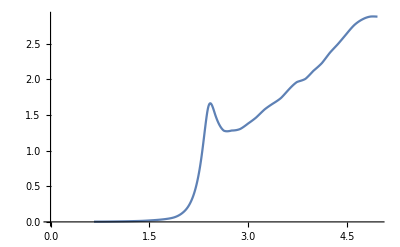

```mathematica
ListLinePlot[Transpose[{data[[All,2]],data[[All,3]]}]]
```

### Ag NP

#### (variating r )

```mathematica
color = {Blue, Red,Orange, Green, Purple, Pink}
(*orden = Table[i,{i,50,300,50}];*)
radio  = 1*^3  {1.,.5,.25,.1}
```

{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0.5, 0],RGBColor[0, 1, 0],RGBColor[0.5, 0, 0.5],RGBColor[1, 0.5, 0.5]}

{1000.,500.,250.,100.}

```mathematica
AbsoluteTiming[Table[{h c /(λ),extCQn[{1.,nAgFunc[λ]},λ,#]},{λ,188.,1935.}]]&/@radio;
tiempo = %[[All,1]];
res = %%[[All,2]];
```

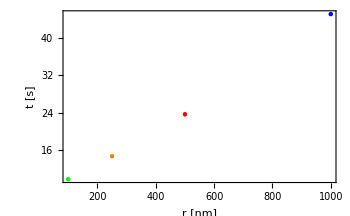
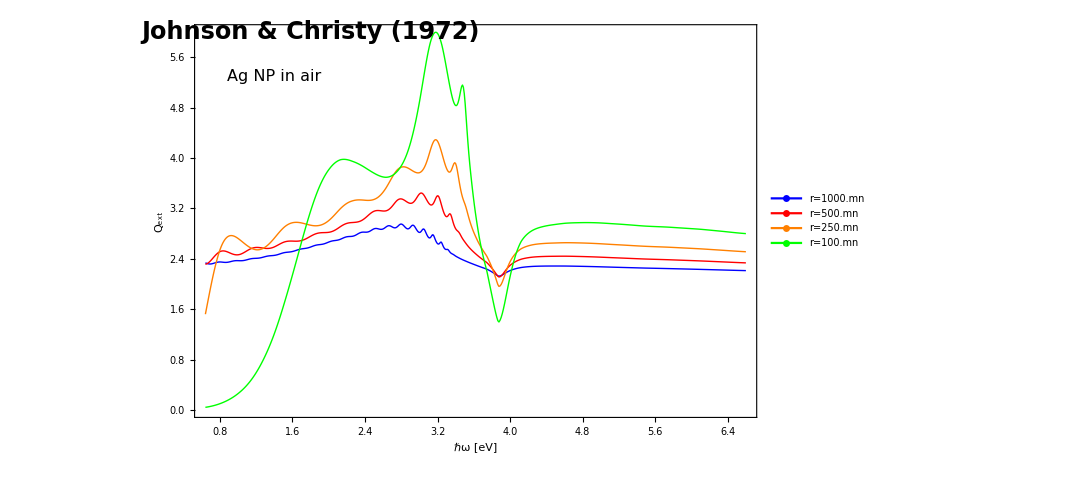

Ag_nVar_radii.pdf

```mathematica
Show[ListLinePlot[res, PlotStyle->Table[{Thick,color[[i]]},{i,Length[color]}],PlotRange->All,
	PlotLegends->legendSquare[Table["r="<>ToString[radio[[i]]]<>"mn",{i,Length[radio]}],"Row",{Right,Bottom}]],
		Frame-> True, 
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["Q_ext",24,Bold],Null},{Style["ℏω [eV]",24, Bold], Null}}, 
		ImageSize-> 800,
		Epilog->{Inset[Style["Johnson & Christy (1972)", 24, Bold], {1.8,6}],
			Inset[Style["Ag NP in air", 16], {1.4,5.3}]}];

Show[ListPlot[Table[{{radio[[i]],tiempo[[i]]}},{i,Length[tiempo]}],PlotStyle->Table[{PointSize[Large],color[[i]]},{i,Length[color]}]],
		Frame-> True,PlotRange-> All,
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["t [s]",24,Bold],Null},{Style["r [nm]",24, Bold], Null}}, 
		ImageSize-> 350];

Overlay[{%,%%},Alignment->{Right,Top}]
Export["Ag_nVar_radii.pdf",%]
```

### n=2 NP

#### (variating r )

```mathematica
color = {Blue, Red,Orange, Green, Purple, Pink}
(*orden = Table[i,{i,50,300,50}];*)
radio  =   {3,5,7,9}
```

{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0.5, 0],RGBColor[0, 1, 0],RGBColor[0.5, 0, 0.5],RGBColor[1, 0.5, 0.5]}

{3,5,7,9}

```mathematica
ext = Table[{λ,extCQn[{1.,2.},λ,#]},{λ,0.,1935.}]&/@radio;
sca = Table[{λ,scaCQn[{1.,2.},λ,#]},{λ,0.,1935.}]&/@radio;
```

```mathematica
abs = Table[{sca[[i,j,1]],ext[[i,j,2]]-sca[[i,j,2]]},{i,Length[sca]},{j,Length[sca[[i]]]}];
```

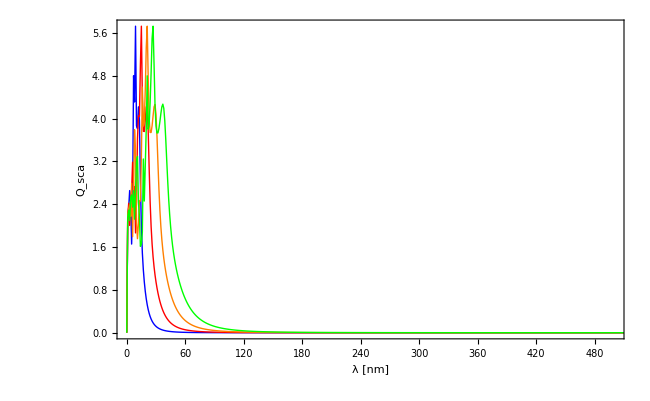
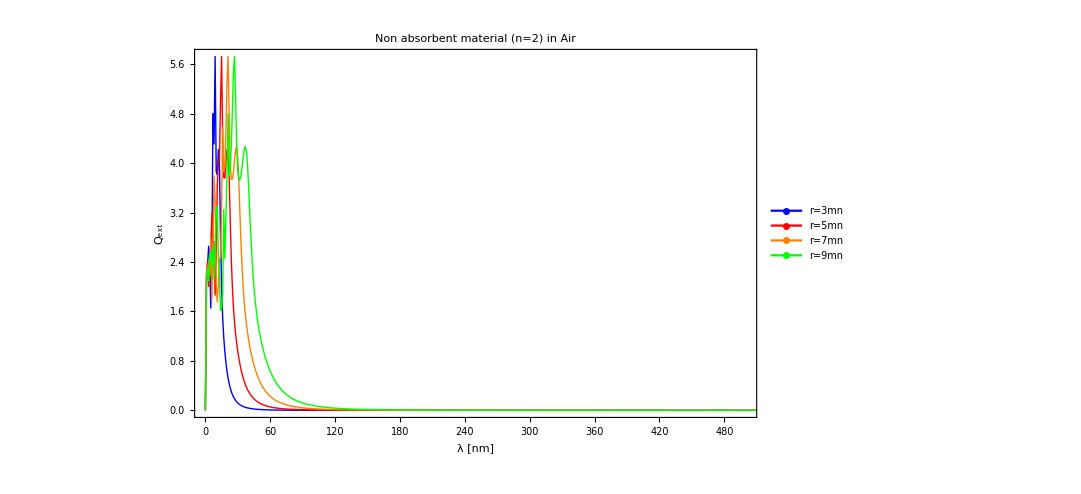
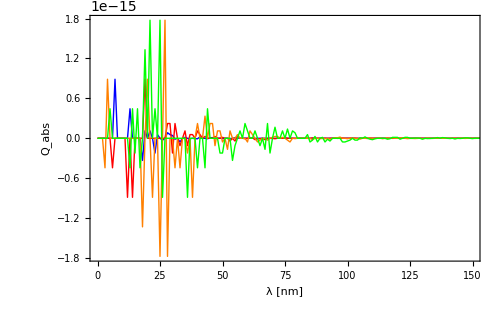

small_nonabsrobent.pdf

```mathematica
Show[ListLinePlot[ext, PlotStyle->Table[{Thick,color[[i]]},{i,Length[color]}],PlotRange->{{0,500},{All,All}},
	PlotLegends->legendSquare[Table["r="<>ToString[radio[[i]]]<>"mn",{i,Length[radio]}],"Row",{Right,Top}]],
		Frame-> True, 
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["Q_ext",24,Bold],Null},{Style["λ [nm]",24, Bold], Null}}, 
		ImageSize-> 800, 
PlotLabel -> Style["Non absorbent material (n=2) in Air", 24, Bold,Black]];

Show[ListLinePlot[sca, PlotStyle->Table[{Thick,color[[i]]},{i,Length[color]}],PlotRange->{{0,500},{All,All}}],
		Frame-> True, 
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["Q_sca",24,Bold],Null},{Style["λ [nm]",24, Bold], Null}}, 
		ImageSize-> 650];

Show[ListLinePlot[abs, PlotStyle->Table[{Thick,color[[i]]},{i,Length[color]}],PlotRange->{{0,150},{All,All}}],
		Frame-> True, 
		FrameStyle-> Directive[Black,Thickness[0.0035]],FrameTicksStyle->Directive[16,Bold],
		FrameLabel->{{Style["Q_abs",24,Bold],Null},{Style["λ [nm]",24, Bold], Null}}, 
		ImageSize-> 500];

Overlay[{%%,%%%,%},Alignment->{.9,.1}]
Export["small_nonabsrobent.pdf",%, ImageResolution-> 500]
```

### Multipole position

```mathematica
color = {Blue, Red,Orange, Green, Purple, Pink};
order = {1,2,3};
radio = 30;
```

```mathematica
nDAu[λ_]:= Sqrt[ 1- (λ/(288.5^2))*(1/(1/λ+I/8270))];
```

```mathematica
drudeExt = Table[{λ,extCQn[{1.,nDAu[λ]},λ,radio]},{λ,200.,700.}];
drudeScat = Table[{λ,scaCQn[{1.,nDAu[λ]},λ,radio]},{λ,200.,700.}];
drudeExtN = Table[{ λ,If[#>1, 10*extCQnFixed[#,{1.,nDAu[λ]},λ,radio],extCQnFixed[#,{1.,nDAu[λ]},λ,radio]]},{λ,200.,700.}]&/@order;
```

```mathematica
Select[drudeExtN[[1]],#[[2]] == Max[drudeExtN[[1,All,2]]] &]
Select[drudeExtN[[2]],#[[2]] == Max[drudeExtN[[2,All,2]]] &]
```

{{526.,15.9977}}

{{462.,4.03147}}

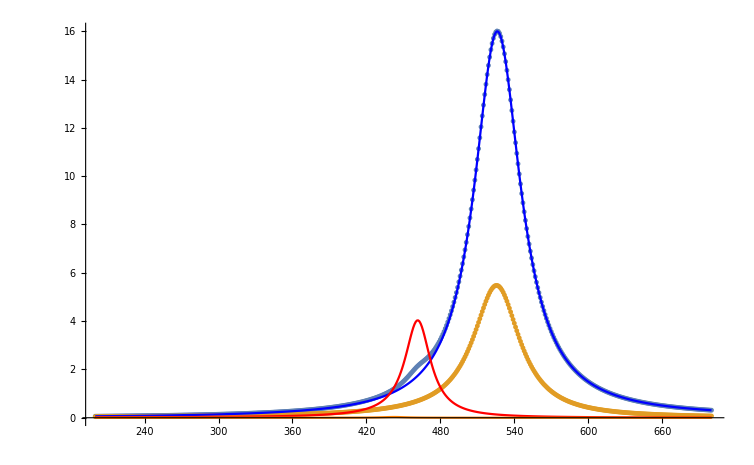

```mathematica
Show[{ListPlot[{drudeExt,drudeScat}, PlotRange->All],ListLinePlot[drudeExtN,PlotStyle->color,PlotRange->All]}]
```

```mathematica
nDAu[λ_]:= Sqrt[ 1- (λ/(123.98^2))*(1/(1/λ+I/8270))];  (*Sometimes it shoud be changed*)
```

```mathematica
drudeExt = Table[{λ,extCQn[{1.,nDAu[λ]},λ,radio]},{λ,150.,700.}];
drudeScat = Table[{λ,scaCQn[{1.,nDAu[λ]},λ,radio]},{λ,150.,700.}];
drudeExtN = Table[{ λ,If[#>1, extCQnFixed[#,{1.,nDAu[λ]},λ,radio],extCQnFixed[#,{1.,nDAu[λ]},λ,radio]]},{λ,150.,700.}]&/@order;
```

```mathematica
Select[drudeExtN[[1]],#[[2]] == Max[drudeExtN[[1,All,2]]] &]
Select[drudeExtN[[2]],#[[2]] == Max[drudeExtN[[2,All,2]]] &]
Select[drudeExtN[[3]],#[[2]] == Max[drudeExtN[[3,All,2]]] &]
```

{{265.,10.6675}}

{{211.,5.42983}}

{{195.,0.384072}}

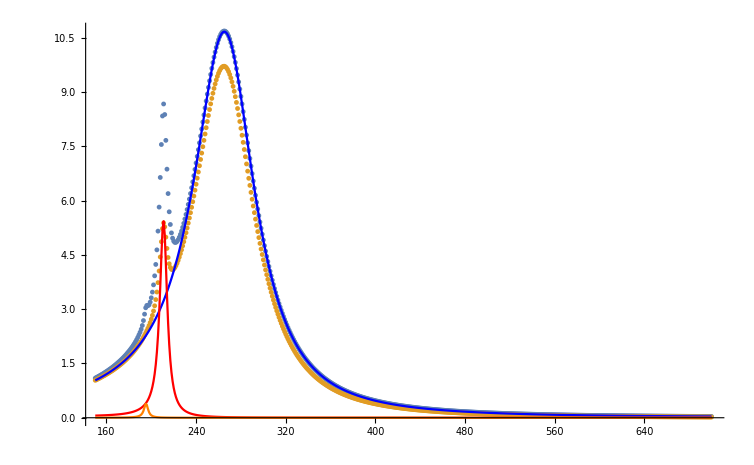

```mathematica
Show[{ListPlot[{drudeExt,drudeScat}, PlotRange->All],ListLinePlot[drudeExtN,PlotStyle->color,PlotRange->All]}]
```

```mathematica
oro = Table[{λ,extCQn[{1.,nAuFunc[λ]},λ,radio]},{λ,200.,700.}](*&/@orden;*);
plata =  Table[{ λ,extCQn[{1.,nAgFunc[λ]},λ,radio]},{λ,200.,500.}](*&/@orden*);
```

```mathematica
oroN = Table[{ λ,If[#>1, 100*extCQnFixed[#,{1.,nAuFunc[λ]},λ,radio],extCQnFixed[#,{1.,nAuFunc[λ]},λ,radio]]},{λ,200.,700.}]&/@order;
plataN =  Table[{λ, If[#>1, 10*extCQnFixed[#,{1.,nAgFunc[λ]},λ,radio],extCQnFixed[#,{1.,nAgFunc[λ]},λ,radio]]},{λ,200.,500.}]&/@order;
```

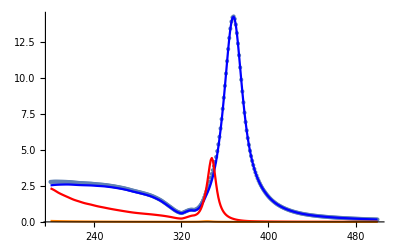
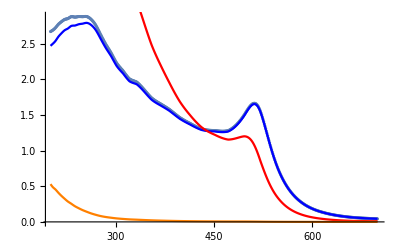

```mathematica
Row[{Show[{ListPlot[plata, PlotRange->All],ListLinePlot[plataN,PlotStyle->color,PlotRange->All]}],Show[{ListPlot[oro, PlotRange->All],ListLinePlot[oroN,PlotStyle->color]}]}]
```

```mathematica
nDAu[λ_]:= Sqrt[ 1- (λ/(288.5^2))*(1/(1/λ+I/8270))];
```

```mathematica
radio = 3
```

3

```mathematica
drudeExt = Table[{λ,extCQn[{1.,nDAu[λ]},λ,radio]},{λ,200.,700.}];
drudeScat = Table[{λ,scaCQn[{1.,nDAu[λ]},λ,radio]},{λ,200.,700.}];
drudeExtN = Table[{ λ,If[#>1, 100*extCQnFixed[#,{1.,nDAu[λ]},λ,radio],extCQnFixed[#,{1.,nDAu[λ]},λ,radio]]},{λ,200.,700.}]&/@order;
```

```mathematica
Select[drudeExtN[[1]],#[[2]] == Max[drudeExtN[[1,All,2]]] &]
Select[drudeExtN[[2]],#[[2]] == Max[drudeExtN[[2,All,2]]] &]
```

{{500.,2.49501}}

{{456.,0.0426476}}

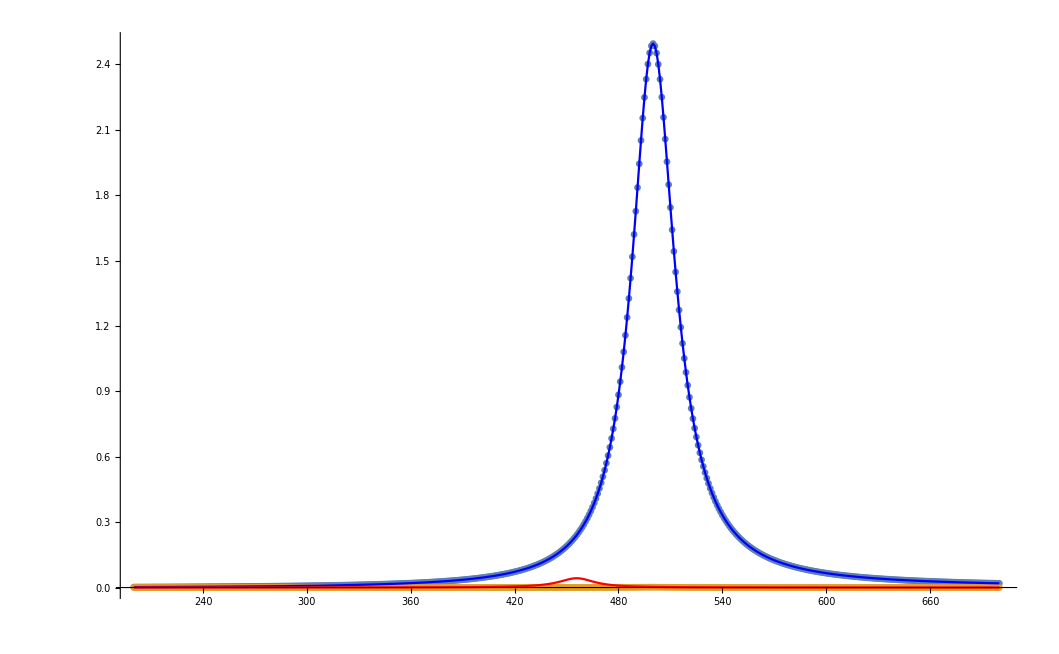

```mathematica
Show[{ListPlot[{drudeExt,drudeScat}, PlotRange->All],ListLinePlot[drudeExtN,PlotStyle->color,PlotRange->All]}]
```

```mathematica
radio = 5
```

5

```mathematica
drudeExt = Table[{λ,extCQn[{1.,nDAu[λ]},λ,radio]},{λ,200.,700.}];
drudeScat = Table[{λ,scaCQn[{1.,nDAu[λ]},λ,radio]},{λ,200.,700.}];
drudeExtN = Table[{ λ,If[#>1, 10*extCQnFixed[#,{1.,nDAu[λ]},λ,radio],extCQnFixed[#,{1.,nDAu[λ]},λ,radio]]},{λ,200.,700.}]&/@order;
```

```mathematica
Select[drudeExtN[[1]],#[[2]] == Max[drudeExtN[[1,All,2]]] &]
Select[drudeExtN[[2]],#[[2]] == Max[drudeExtN[[2,All,2]]] &]
```

{{500.,4.14312}}

{{456.,0.0197292}}

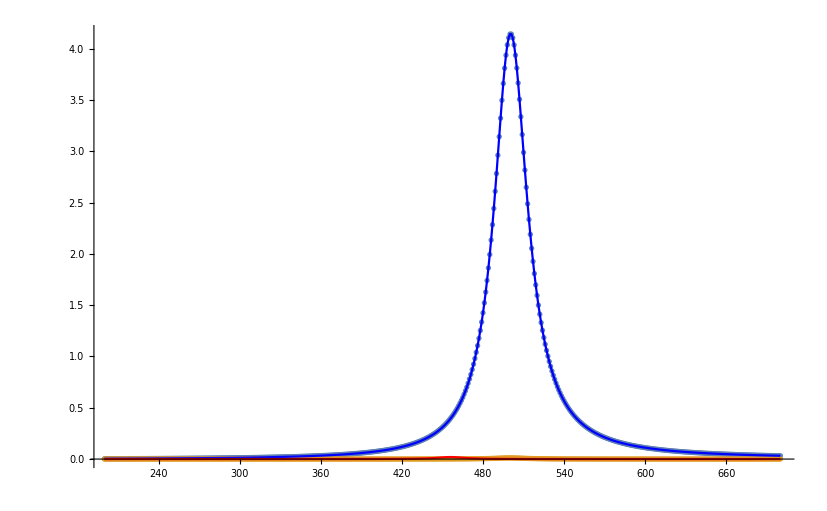

```mathematica
Show[{ListPlot[{drudeExt,drudeScat}, PlotRange->All],ListLinePlot[drudeExtN,PlotStyle->color,PlotRange->All]}]
```

```mathematica
radio = 10
```

10

```mathematica
drudeExt = Table[{λ,extCQn[{1.,nDAu[λ]},λ,radio]},{λ,200.,700.}];
drudeScat = Table[{λ,scaCQn[{1.,nDAu[λ]},λ,radio]},{λ,200.,700.}];
drudeExtN = Table[{ λ,If[#>1, 10*extCQnFixed[#,{1.,nDAu[λ]},λ,radio],extCQnFixed[#,{1.,nDAu[λ]},λ,radio]]},{λ,200.,700.}]&/@order;
```

```mathematica
Select[drudeExtN[[1]],#[[2]] == Max[drudeExtN[[1,All,2]]] &]
Select[drudeExtN[[2]],#[[2]] == Max[drudeExtN[[2,All,2]]] &]
```

{{503.,8.12174}}

{{456.,0.157001}}

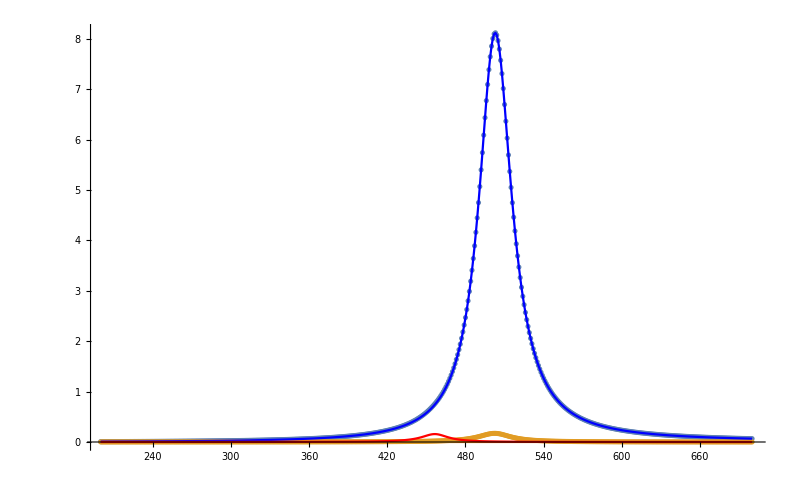

```mathematica
Show[{ListPlot[{drudeExt,drudeScat}, PlotRange->All],ListLinePlot[drudeExtN,PlotStyle->color,PlotRange->All]}]
```

```mathematica
radio = 20
```

20

```mathematica
drudeExt = Table[{λ,extCQn[{1.,nDAu[λ]},λ,radio]},{λ,200.,700.}];
drudeScat = Table[{λ,scaCQn[{1.,nDAu[λ]},λ,radio]},{λ,200.,700.}];
drudeExtN = Table[{ λ,If[#>1, 10*extCQnFixed[#,{1.,nDAu[λ]},λ,radio],extCQnFixed[#,{1.,nDAu[λ]},λ,radio]]},{λ,200.,700.}]&/@order;
```

```mathematica
Select[drudeExtN[[1]],#[[2]] == Max[drudeExtN[[1,All,2]]] &]
Select[drudeExtN[[2]],#[[2]] == Max[drudeExtN[[2,All,2]]] &]
```

{{512.,14.1154}}

{{458.,1.23507}}

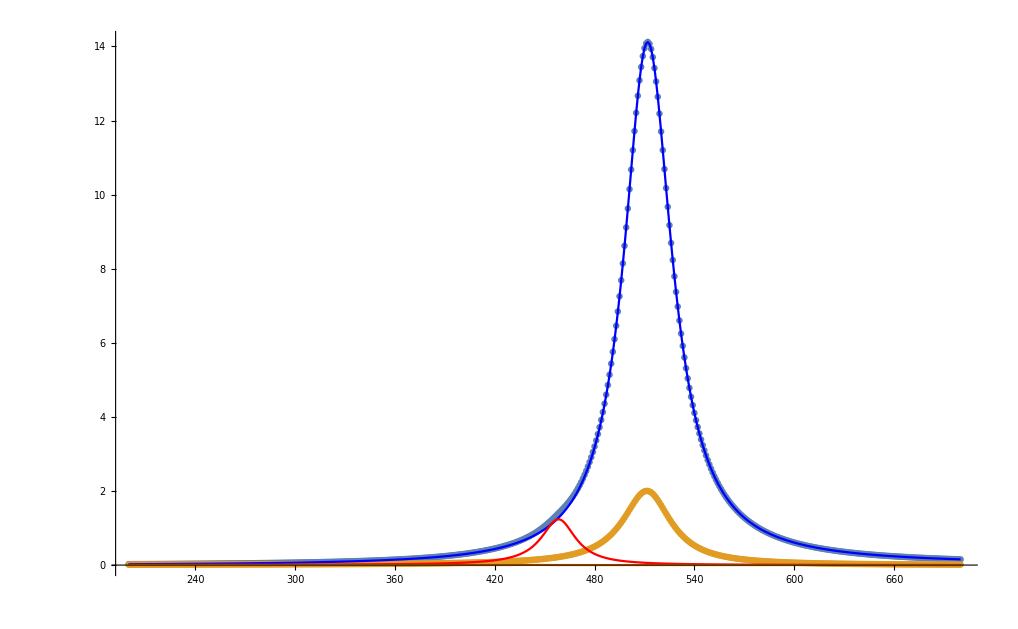

```mathematica
Show[{ListPlot[{drudeExt,drudeScat}, PlotRange->All],ListLinePlot[drudeExtN,PlotStyle->color,PlotRange->All]}]
```

## π_n & τ_n functions

```mathematica
pi[n_,θ_]:=Module[{f},
f[0]=0;f[1]=1;  
f[i_]:=f[i]=(2 i -1)/(i-1)Cos[θ]f[i-1]-i/(i-1)f[i-2];
f[n]]
tau[n_,θ_]:=Module[{f},
f[0]=0;f[1]=1;
f[i_]:=f[i]=(2 i -1)/(i-1)Cos[θ]f[i-1]-i/(i-1)f[i-2];
 n Cos[θ] f[n] - (n+1)f[n-1]]
```

```mathematica
color = {Blue, Red,Orange, Green, Purple, Pink};
PolarPlot[{pi[#,t],tau[#,t]},{t,0,2π},PlotStyle-> {{Red,Thick},{Blue,Thick}},
PlotTheme->"Business",PlotLabel-> "n="<>ToString[#],ImageSize->400]&/@Table[i,{i, Length[color]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Scattering Matrix elements

```mathematica
s1[indexes_,λ_,rad_,θ_]:= Module[{x, nmax,an,bn},
x = 2* π *indexes[[1]] *rad / λ;
nmax =  Round[x+4 x^(1/3)+2];
{an,bn} = mieCoef[Table[i,{i,nmax}],indexes,λ,rad];
Sum[(2 i +1)/(i(i+1))(an[[i]]  pi[i,θ]+bn[[i]] tau[i,θ]),{i,Length[an]}]]
```

```mathematica
s2[indexes_,λ_,rad_,θ_]:= Module[{x, nmax,an,bn},
x = 2* π *indexes[[1]] *rad / λ;
nmax =  Round[x+4 x^(1/3)+2];
{an,bn} = mieCoef[Table[i,{i,nmax}],indexes,λ,rad];
Sum[(2 i +1)/(i(i+1))(an[[i]]  tau[i,θ]+bn[[i]] pi[i,θ]),{i,Length[an]}]]
```

```mathematica
s0[indexes_,λ_,rad_,θ_]:= Module[{x, nmax,an,bn},
x = 2* π *indexes[[1]] *rad / λ;
nmax =  Round[x+4 x^(1/3)+2];
{an,bn} = mieCoef[Table[i,{i,nmax}],indexes,λ,rad];
0.5*Sum[(2 i +1)*(an[[i]] +bn[[i]]),{i,Length[an]}]]
```

## Vectorial Spherical Harmonics

```mathematica
(*En la base de Subscript[e, θ]= {1,0} y Subscript[e, φ]= {0,1}*)

Mo1n[ρ_,θ_,φ_,n_]:= Cos[φ]pi[n,θ]SphericalHankelH1[n,ρ]{1,0}-Sin[φ]tau[n,θ]SphericalHankelH1[n,ρ]{0,1}

Me1n[ρ_,θ_,φ_,n_]:= -Sin[φ]pi[n,θ]SphericalHankelH1[n,ρ]{1,0}-Cos[φ]tau[n,θ]SphericalHankelH1[n,ρ]{0,1};

No1n[ρ_,θ_,φ_,n_]:= Sin[φ]tau[n,θ](-n *SphericalHankelH1[n,ρ]+ρ*SphericalHankelH1[n-1,ρ])(1/ρ){1,0}+Cos[φ]pi[n,θ](-n *SphericalHankelH1[n,ρ]+ρ*SphericalHankelH1[n-1,ρ])(1/ρ){0,1};

Ne1n[ρ_,θ_,φ_,n_]:=Cos[φ]tau[n,θ](-n *SphericalHankelH1[n,ρ]+ρ*SphericalHankelH1[n-1,ρ])(1/ρ){1,0}-Sin[φ]pi[n,θ](-n *SphericalHankelH1[n,ρ]+ρ*SphericalHankelH1[n-1,ρ])(1/ρ){0,1};
```

```mathematica
fontsize = 40;
axislabelPos = 1.75;
SHVlabelPos = 2;
```

```mathematica
axes3DArrow = {Black,Opacity[1],Thick,Arrowheads[Large],Arrow[{{{0,0,0},{0,0,1.5}},{{0,0,0},{0,1.5,0}},{{0,0,0},{1.5,0,0}}}],Inset[MaTeX["z",FontSize->fontsize],{0,0,axislabelPos}],Inset[MaTeX["y",FontSize->fontsize],{0,axislabelPos,0}],Inset[MaTeX["x",FontSize->fontsize],{axislabelPos,0,0}]};

twoaxes3DArrow =  {Black,Opacity[1],Thick,Arrowheads[Large],Arrow[{{{0,0,0},{0,0,1.5}},{{0,0,0},{1.5,0,0}}}],Inset[MaTeX["z",FontSize->fontsize],{0,0,axislabelPos}],Inset[MaTeX["x",FontSize->fontsize],{axislabelPos,0,0}]};
```

### Ne11 & Mo11

```mathematica
Table[{{θ,φ},I*Ne1n[2,θ,φ,1]//Re},{φ,-π,π,.1},{θ,0,π,.1}];
sp=ListStreamPlot[%,ColorFunctionScaling->True,StreamColorFunction->(ColorData["Rainbow",#5]&),StreamPoints-> Fine];

norm =Show[{Graphics3D[{twoaxes3DArrow,Inset[MaTeX["a_1:\\mathbf{E}^s\\propto i\\mathbf{N}_{e11}",FontSize->fontsize],{0,0,SHVlabelPos}]}],SphericalPlot3D[Norm[Ne1n[2,θ,φ,1]],{θ,0,π},{φ,-π,π},ColorFunctionScaling-> True,ColorFunction->Function[{x,y,z,θ,Φ,r},ColorData["Rainbow"][r]],ColorFunctionScaling->True,Mesh->False,Axes->False]},
Boxed->False,ImageSize->350];

Show[{norm,
Graphics3D[{sp[[1]]/.Arrow[z_]:>Arrow[z/.{y_Real,x_Real}:>{Cos[x] Sin[y],Sin[y] Sin[x],Cos[y]}],
	Opacity[.5],Black,Sphere[]}]},SphericalRegion->True,ViewVector-> {5 {Cos[t],Sin[t],0},{0,0,0}}/.t-> Pi/2,Boxed->False,ImageSize-> 800]

(*Manipulate[Show[{norm,
Graphics3D[{sp[[1]]/.Arrow[z_]:>Arrow[z/.{y_Real,x_Real}:>{Cos[x] Sin[y],Sin[y] Sin[x],Cos[y]}],
	Opacity[.5],Black,Sphere[]}]},SphericalRegion->True,ViewVector->Dynamic[{5 {Cos[t],Sin[t],.25},{0,0,0}},None],Boxed->False,ImageSize-> 800],{t,0, 2π,.1}]*)
```

-Graphics3D-

```mathematica
Table[{{θ,φ},-Mo1n[2,θ,φ,1]//Re},{φ,-π,π,.1},{θ,0,π,.1}];
sp=ListStreamPlot[%,ColorFunctionScaling->True,StreamColorFunction->(ColorData["Rainbow",#5]&),StreamPoints-> Fine];

norm =Show[{Graphics3D[{axes3DArrow,Inset[MaTeX["a_1:\\mathbf{E}^s\\propto -\\mathbf{M}_{o11}",FontSize->fontsize],{0,0,SHVlabelPos}]}],SphericalPlot3D[Norm[Mo1n[2,θ,φ,1]],{θ,0,π},{φ,-π,π},ColorFunctionScaling-> True,ColorFunction->Function[{x,y,z,θ,Φ,r},ColorData["Rainbow"][r]],ColorFunctionScaling->True,Mesh->False,Axes->False]},
Boxed->False,ImageSize->350];

(*Show[{norm,
Graphics3D[{sp[[1]]/.Arrow[z_]:>Arrow[z/.{y_Real,x_Real}:>{Cos[x] Sin[y],Sin[y] Sin[x],Cos[y]}],
	Opacity[.5],Black,Sphere[]}]},SphericalRegion->True,ViewVector-> {5 {Cos[t],Sin[t],.25},{0,0,0}}/.t-> Pi/4,Boxed->False,ImageSize-> 800]*)

Manipulate[Show[{norm,
Graphics3D[{sp[[1]]/.Arrow[z_]:>Arrow[z/.{y_Real,x_Real}:>{Cos[x] Sin[y],Sin[y] Sin[x],Cos[y]}],
	Opacity[.5],Black,Sphere[]}]},SphericalRegion->True,ViewVector->Dynamic[{5 {Cos[t],Sin[t],.25},{0,0,0}},None],Boxed->False,ImageSize-> 800],{t,0, 2π,.1}]
```

### Statics for n = 1,2,3,4

```mathematica
listNe = {};
listMo = {};

For[i =1,i≤ 4,i++,
CreateDirectory[FileNameJoin[{"1.- Gifs","Ne1"<>ToString[i]}]];
data =Table[{{θ,φ},I*Ne1n[2,θ,φ,i]//Re},{φ,0,π,.1},{θ,0,π,.1}];
sp=ListStreamPlot[data,ColorFunctionScaling->True,StreamColorFunction->(ColorData["Rainbow",#5]&),StreamPoints-> Fine];

axes =Show[{Graphics3D[{twoaxes3DArrow,Inset[MaTeX["a_"<>ToString[i]<>":\\mathbf{E}^s\\propto i\\mathbf{N}_{e,1,"<>ToString[i]<>"}",FontSize->fontsize],{0,0,SHVlabelPos}]}]},
Boxed->False,ImageSize->350];

 AppendTo[listNe,Show[{axes,
					Graphics3D[{sp[[1]]/.Arrow[z_]:>Arrow[z/.{y_Real,x_Real}:>{Cos[x] Sin[y],Sin[y] Sin[x],Cos[y]}],Opacity[.75],Black,Sphere[]}]},
				SphericalRegion->True,ViewVector-> {5 {Cos[t],Sin[t],0}/. t-> π/2,{0,0,0}},Boxed->False,ImageSize-> 800]				
		];
(**********************)
CreateDirectory[FileNameJoin[{"1.- Gifs","Mo1"<>ToString[i]}]];
data = Table[{{θ,φ},-Mo1n[2,θ,φ,i]//Re},{φ,0,π,.1},{θ,0,π,.1}];
sp=ListStreamPlot[data,ColorFunctionScaling->True,StreamColorFunction->(ColorData["Rainbow",#5]&),StreamPoints-> Fine];

axes =Show[{Graphics3D[{twoaxes3DArrow,Inset[MaTeX["b_"<>ToString[i]<>":\\mathbf{E}^s\\propto -\\mathbf{M}_{o,1,"<>ToString[i]<>"}",FontSize->fontsize],{0,0,SHVlabelPos}]}]},
Boxed->False,ImageSize->350];

 AppendTo[listMo,
				Show[{axes,
						Graphics3D[{sp[[1]]/.Arrow[z_]:>Arrow[z/.{y_Real,x_Real}:>{Cos[x] Sin[y],Sin[y] Sin[x],Cos[y]}],Opacity[.75],Black,Sphere[]}]},
					SphericalRegion->True,ViewVector-> {5 {Cos[t],Sin[t],0},{0,0,0}}/. t-> π/2,Boxed->False,ImageSize-> 800]
		]
]

ClearAll[i];
```

CreateDirectory::filex: /home/jonathan/Dropbox/Escuela/3.- Tesis/2.- Notas generales/2.- Teoría de Mie/0.- Cálculos/1.- Gifs/Ne11 already exists.

CreateDirectory::filex: /home/jonathan/Dropbox/Escuela/3.- Tesis/2.- Notas generales/2.- Teoría de Mie/0.- Cálculos/1.- Gifs/Mo11 already exists.

CreateDirectory::filex: /home/jonathan/Dropbox/Escuela/3.- Tesis/2.- Notas generales/2.- Teoría de Mie/0.- Cálculos/1.- Gifs/Ne12 already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

```mathematica
Export[FileNameJoin[{"1.- Gifs","Ne1"<>ToString[#],"Ne1"<>ToString[#]<>"_static.png"}],listNe[[#]],"AnimationRepetitions"->∞]&/@Table[i,{i,Length[listNe]}]
Export[FileNameJoin[{"1.- Gifs","Mo1"<>ToString[#],"Mo1"<>ToString[#]<>"_static.png"}],listMo[[#]],"AnimationRepetitions"->∞]&/@Table[i,{i,Length[listMo]}]
```

{1.- Gifs/Ne11/Ne11_static.png,1.- Gifs/Ne12/Ne12_static.png,1.- Gifs/Ne13/Ne13_static.png,1.- Gifs/Ne14/Ne14_static.png}

{1.- Gifs/Mo11/Mo11_static.png,1.- Gifs/Mo12/Mo12_static.png,1.- Gifs/Mo13/Mo13_static.png,1.- Gifs/Mo14/Mo14_static.png}

### Gifs for n = 1,2,3,4

```mathematica
gifslistNe = {};
gifslistMo = {};

For[i =1,i≤ 4,i++,
CreateDirectory[FileNameJoin[{"1.- Gifs","Ne1"<>ToString[i]}]];
data =Table[{{θ,φ},I*Ne1n[2,θ,φ,i]//Re},{φ,-π,π,.1},{θ,0,π,.1}];
sp=ListStreamPlot[data,ColorFunctionScaling->True,StreamColorFunction->(ColorData["Rainbow",#5]&),StreamPoints-> Fine];

axes =Show[{Graphics3D[{axes3DArrow,Inset[MaTeX["a_"<>ToString[i]<>":\\mathbf{E}^s\\propto i\\mathbf{N}_{e,1,"<>ToString[i]<>"}",FontSize->fontsize],{0,0,SHVlabelPos}]}]},
Boxed->False,ImageSize->350];

 AppendTo[gifslistNe,
				Table[Show[{axes,
						Graphics3D[{sp[[1]]/.Arrow[z_]:>Arrow[z/.{y_Real,x_Real}:>{Cos[x] Sin[y],Sin[y] Sin[x],Cos[y]}],Opacity[.5],Black,Sphere[]}]},
					SphericalRegion->True,ViewVector-> {5 {Cos[t],Sin[t],.25},{0,0,0}},Boxed->False,ImageSize-> 800],
				{t,0, 2π,.1}]
		];
(**********************)
CreateDirectory[FileNameJoin[{"1.- Gifs","Mo1"<>ToString[i]}]];
data = Table[{{θ,φ},-Mo1n[2,θ,φ,i]//Re},{φ,-π,π,.1},{θ,0,π,.1}];
sp=ListStreamPlot[data,ColorFunctionScaling->True,StreamColorFunction->(ColorData["Rainbow",#5]&),StreamPoints-> Fine];

axes =Show[{Graphics3D[{axes3DArrow,Inset[MaTeX["b_"<>ToString[i]<>":\\mathbf{E}^s\\propto -\\mathbf{M}_{o,1,"<>ToString[i]<>"}",FontSize->fontsize],{0,0,SHVlabelPos}]}]},
Boxed->False,ImageSize->350];

 AppendTo[gifslistMo,
				Table[Show[{axes,
						Graphics3D[{sp[[1]]/.Arrow[z_]:>Arrow[z/.{y_Real,x_Real}:>{Cos[x] Sin[y],Sin[y] Sin[x],Cos[y]}],Opacity[.5],Black,Sphere[]}]},
					SphericalRegion->True,ViewVector-> {5 {Cos[t],Sin[t],.25},{0,0,0}},Boxed->False,ImageSize-> 800],
				{t,0, 2π,.1}]
		]
]

ClearAll[i];
```

CreateDirectory::filex: /home/jonathan/Dropbox/Escuela/3.- Tesis/2.- Notas generales/2.- Teoría de Mie/0.- Cálculos/1.- Gifs/Ne11 already exists.

CreateDirectory::filex: /home/jonathan/Dropbox/Escuela/3.- Tesis/2.- Notas generales/2.- Teoría de Mie/0.- Cálculos/1.- Gifs/Mo11 already exists.

CreateDirectory::filex: /home/jonathan/Dropbox/Escuela/3.- Tesis/2.- Notas generales/2.- Teoría de Mie/0.- Cálculos/1.- Gifs/Ne12 already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

```mathematica
Export[FileNameJoin[{"1.- Gifs","Ne1"<>ToString[#],"Ne1"<>ToString[#]<>".gif"}],gifslistNe[[#]],"AnimationRepetitions"->∞]&/@Table[i,{i,Length[gifslistNe]}]
Export[FileNameJoin[{"1.- Gifs","Mo1"<>ToString[#],"Mo1"<>ToString[#]<>".gif"}],gifslistMo[[#]],"AnimationRepetitions"->∞]&/@Table[i,{i,Length[gifslistMo]}]
```

{1.- Gifs/Ne11/Ne11.gif,1.- Gifs/Ne12/Ne12.gif,1.- Gifs/Ne13/Ne13.gif,1.- Gifs/Ne14/Ne14.gif}

{1.- Gifs/Mo11/Mo11.gif,1.- Gifs/Mo12/Mo12.gif,1.- Gifs/Mo13/Mo13.gif,1.- Gifs/Mo14/Mo14.gif}